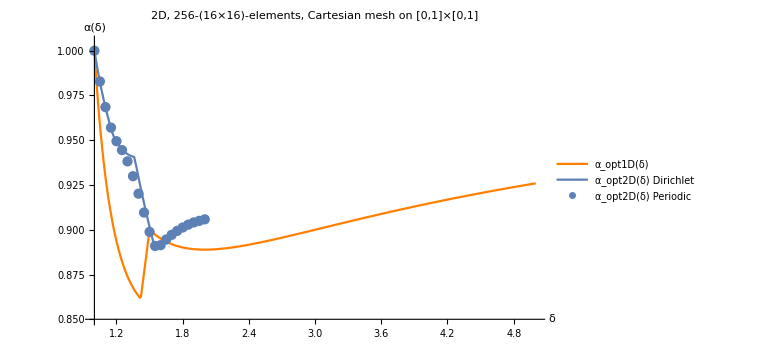

```mathematica
α[δ_]=If[δ<Root[-1+4 #1-8 #1^2+4 #1^3&,1],(δ(-1+2δ))/(-1+2 δ^2),If[δ<3/2,(2 δ^2 (-1+2 δ))/(1+δ (-5+2 δ (2+δ))+δ Abs[1+2 (-2+δ) δ]),(2 δ^2)/(-1+δ+2 δ^2)]];
ρ[δ_]=If[δ>Root[-1+4 #1-8 #1^2+4 #1^3&,1],1+(α[δ] (2+(-2-4 δ)δ+√(4-24 δ+52 δ^2-48 δ^3+16 δ^4)))/(4 δ^2),1+(α[δ] (2-4 δ^2+√(4-32δ+80 δ^2-64 δ^3+16 δ^4)))/(δ (-2+4δ))];
Show[Plot[α[δ],{δ,1,5},PlotRange->{0.85,1.005},ImageSize->Large,AxesLabel->{"δ","α(δ)"},PlotStyle->Orange,PlotLegends->{"α_opt1D(δ)"},PlotLabel->"2D, 256-(16×16)-elements, Cartesian mesh on [0,1]×[0,1]"],
ListPlot[
{
{
{1.0,1},{1.02,0.992517089843751},{1.04,0.9857055664062511},{1.06,0.9794677734375008},{1.08,0.9737243652343759},{1.1,0.9684112548828137},{1.12,0.9634750366210948},{1.1400000000000001,0.9588729858398447},{1.16,0.954566192626954},{1.18,0.9514434814453134},{1.2,0.9491516113281258},{1.22,0.9472152709960948},{1.24,0.9455886840820324},{1.26,0.944238281250001},{1.28,0.9431320190429702},{1.3,0.9422424316406265},{1.32,0.941544342041017},{1.34,0.9410186767578137},{1.3599999999999999,0.9406463623046886},{1.38,0.9352951049804694},{1.4,0.9291610717773447},{1.42,0.923255157470704},{1.44,0.9175567626953135},{1.46,0.9120491027832043},{1.48,0.9067153930664074},{1.5,0.9015426635742197},{1.52,0.896520996093751},{1.54,0.8916412353515628},{1.56,0.8896652221679692},{1.58,0.8910644531250005},{1.6,0.8923789978027352},{1.62,0.8936141967773444},{1.6400000000000001,0.8947746276855482},{1.6600000000000001,0.895864868164064},{1.6800000000000002,0.8968902587890635},{1.7,0.8978546142578134},{1.72,0.8987625122070318},{1.74,0.8996192932128916},{1.76,0.900427246093751},{1.78,0.9011917114257821},{1.8,0.9019149780273447},{1.8199999999999998,0.9026016235351576},{1.8399999999999999,0.9032539367675789},{1.8599999999999999,0.9038757324218758},{1.88,0.9044692993164072},{1.9,0.9050369262695322},{1.92,0.9055809020996115},{1.94,0.906104278564454},{1.96,0.9066070556640634},{1.98,0.907093048095704},{2.0,0.9075096130371103}(*,{2.5,0.9131690979003904},{3.0,0.916316223144531},{3.5,0.9207565307617187},{4.0,0.9256393432617189},{4.5,0.9303665161132809},{5.0,0.9347412109375002},{5.5,0.938720703125},{6.0,0.9423141479492188},{6.5,0.9455551147460936},{7.0,0.9484832763671875},{7.5,0.9511322021484376},{8.0,0.9535362243652341},{8.5,0.9557250976562499},{9.0,0.9577255249023438},{9.5,0.9595581054687503},{10.0,0.9612426757812498}*)
}
}
,Joined->True,PlotLegends->{"α_opt2D(δ) Dirichlet"}],
ListPlot[
{
{
{1.0,1},{1.05,0.9828125000000002},{1.1,0.9684936523437502},{1.15,0.95703125},{1.2,0.94945068359375},{1.25,0.9444885253906249},{1.3,0.93819580078125},{1.35,0.9299194335937497},{1.4,0.9201416015625001},{1.45,0.9096008300781249},{1.5,0.8988098144531249},{1.55,0.8909301757812499},{1.6,0.8913818359374999},{1.65,0.89451904296875},{1.7,0.8971618652343748},{1.75,0.8993713378906251},{1.8,0.9012451171875},{1.85,0.9028503417968748},{1.9,0.9041015625},{1.95,0.9049621582031249},{2.0,0.9058105468749997}(*,{2.2,0.91},{2.4,0.914},{2.6,0.915},{2.8,0.917},{3,0.919},{3.2,0.921},{3.4,0.924},{3.6,0.926},{3.8,0.929},{4,0.931},{4.2,0.933},{4.4,0.935},{4.6,0.937},{4.8,0.939},{5,0.941}*)
}
},PlotLegends->{"α_opt2D(δ) Periodic"}
](*,
ListPlot[
{
{
{1.0,1},{1.05,0.985936},{1.1,0.976486},{1.15,0.970318},{1.2,0.966855},{1.25,0.962763},{1.3,0.956193},{1.35,0.947406},{1.4,0.936712},{1.45,0.927488},{1.5,0.918635},{1.55,0.909686},{1.6,0.902146},{1.65,0.900088},{1.7,0.901102},{1.75,0.901958},{1.8,0.903108},{1.85,0.90388},{1.9,0.904563},{1.95,0.905038},{2,0.905671},{2.2,0.906},{2.4,0.908},{2.6,0.91},{2.8,0.913},{3,0.917},{3.2,0.92},{3.4,0.923},{3.6,0.925},{3.8,0.928},{4,0.931},{4.2,0.933},{4.4,0.934},{4.6,0.937},{4.8,0.939},{5,0.941}
}
},PlotLegends->{"α_opt3D(δ) Dirichlet"},PlotStyle->Darker[Green]
]*)
]
```

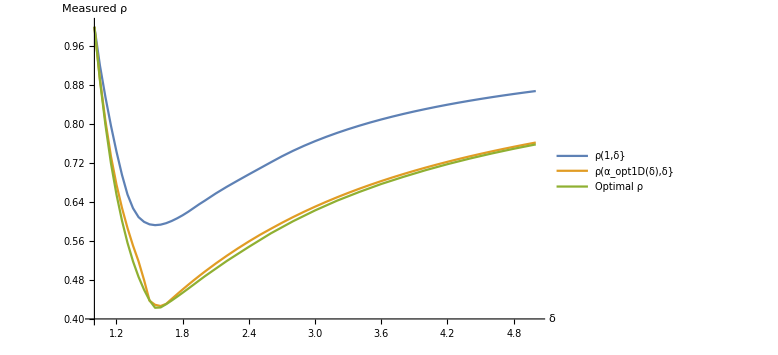

```mathematica
ListPlot[
{
{
{1,1},{1.05,0.92053},{1.1,0.855529},{1.15,0.796856},{1.2,0.743696},{1.25,0.695837},{1.3,0.655508},{1.35,0.627337},{1.4,0.6091},{1.45,0.599334},{1.5,0.594234},{1.55,0.592597},{1.6,0.593616},{1.65,0.596645},{1.7,0.601137},{1.75,0.606677},{1.8,0.612949},{1.85,0.620025},{1.9,0.627803},{1.95,0.635607},{2,0.64277},{2.1,0.657713},{2.2,0.671405},{2.3,0.684278},{2.4,0.696927},{2.5,0.709364},{2.6,0.721807},{2.7,0.734024},{2.8,0.745245},{2.9,0.755566},{3,0.765087},{3.1,0.773907},{3.2,0.782077},{3.3,0.789689},{3.4,0.796787},{3.5,0.803447},{3.6,0.809661},{3.7,0.815495},{3.8,0.82098},{3.9,0.826148},{4,0.831025},{4.1,0.835635},{4.2,0.839996},{4.3,0.844134},{4.4,0.848062},{4.5,0.851797},{4.6,0.855351},{4.7,0.858738},{4.8,0.86197},{4.9,0.865056},{5,0.868006}
},
{
{1,1},{1.05,0.892837},{1.1,0.806436},{1.15,0.733928},{1.2,0.675872},{1.25,0.628006},{1.3,0.586668},{1.35,0.550433},{1.4,0.518322},{1.45,0.479882},{1.5,0.43727},{1.55,0.429026},{1.6,0.426453},{1.65,0.430961},{1.7,0.440966},{1.75,0.450873},{1.8,0.460586},{1.85,0.470076},{1.9,0.479319},{1.95,0.488324},{2,0.497079},{2.1,0.513874},{2.2,0.529775},{2.3,0.544839},{2.4,0.559124},{2.5,0.572675},{2.6,0.585231},{2.7,0.59749},{2.8,0.609109},{2.9,0.620121},{3,0.630566},{3.1,0.640475},{3.2,0.649875},{3.3,0.658811},{3.4,0.66732},{3.5,0.675414},{3.6,0.683127},{3.7,0.690485},{3.8,0.69751},{3.9,0.704234},{4,0.710658},{4.1,0.716809},{4.2,0.722704},{4.3,0.728366},{4.4,0.733795},{4.5,0.73901},{4.6,0.744023},{4.7,0.748846},{4.8,0.753501},{4.9,0.757977},{5,0.762292}
},
{
{1,1},{1.05,0.890171},{1.1,0.798385},{1.15,0.719647},{1.2,0.65555},{1.25,0.601833},{1.3,0.556297},{1.35,0.518194},{1.4,0.486446},{1.45,0.459965},{1.5,0.438015},{1.55,0.422957},{1.6,0.423604},{1.65,0.430219},{1.7,0.437718},{1.75,0.445657},{1.8,0.453837},{1.85,0.462145},{1.9,0.470575},{1.95,0.479107},{2,0.487504},{2.2,0.519054},{2.4,0.548075},{2.6,0.57589},{2.8,0.600598},{3,0.622878},{3.2,0.642962},{3.4,0.660727},{3.6,0.677168},{3.8,0.691756},{4,0.705375},{4.2,0.717824},{4.4,0.729244},{4.6,0.739751},{4.8,0.749448},{5,0.758422}
}
},Joined->True,PlotRange->{{1,5},{0.4,1.005}},ImageSize->Large,AxesLabel->{"δ","Measured ρ"}(*,PlotLabel->"2D, 256-(16×16)-elements, Cartesian mesh on [0,1]×[0,1]" *), PlotLegends->{"ρ(1,δ}","ρ(α_opt1D(δ),δ}","Optimal ρ"},BaseStyle->{FontSize->20},LabelStyle->Directive[FontSize->20]]
```

```mathematica
N[α[2.]]
```

0.888889

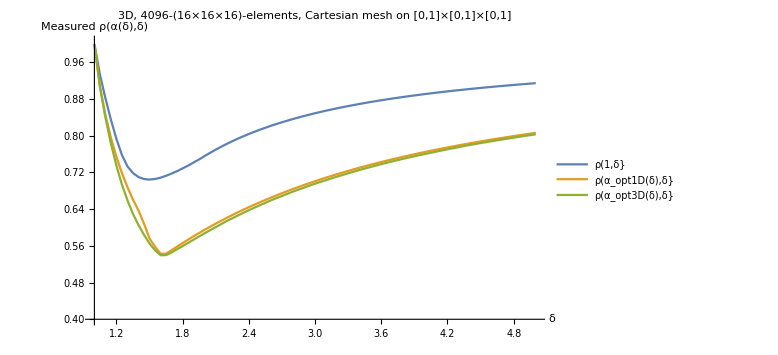

```mathematica
ListPlot[
{
{
{1,1},{1.05,0.933488},{1.1,0.881572},{1.15,0.834745},{1.2,0.792746},{1.25,0.757827},{1.3,0.733068},{1.35,0.718682},{1.4,0.70998},{1.45,0.705645},{1.5,0.704558},{1.55,0.705808},{1.6,0.708741},{1.65,0.712838},{1.7,0.717714},{1.75,0.722975},{1.8,0.729015},{1.85,0.735077},{1.9,0.741873},{1.95,0.74863},{2,0.756094},{2.1,0.769906},{2.2,0.782463},{2.3,0.793791},{2.4,0.80403},{2.5,0.813326},{2.6,0.821792},{2.7,0.829529},{2.8,0.836631},{2.9,0.843168},{3,0.849193},{3.1,0.854785},{3.2,0.859973},{3.3,0.864796},{3.4,0.869302},{3.5,0.873525},{3.6,0.877477},{3.7,0.881186},{3.8,0.884683},{3.9,0.887963},{4,0.891073},{4.1,0.894022},{4.2,0.896819},{4.3,0.899433},{4.4,0.901945},{4.5,0.904329},{4.6,0.906599},{4.7,0.908762},{4.8,0.910833},{4.9,0.912806},{5,0.914693}
},
{
{1,1},{1.05,0.907492},{1.1,0.845448},{1.15,0.795311},{1.2,0.753643},{1.25,0.718241},{1.3,0.687591},{1.35,0.660693},{1.4,0.636804},{1.45,0.608054},{1.5,0.575887},{1.55,0.55798},{1.6,0.54278},{1.65,0.542988},{1.7,0.550653},{1.75,0.558456},{1.8,0.566162},{1.85,0.573716},{1.9,0.581081},{1.95,0.588247},{2,0.595225},{2.1,0.6086},{2.2,0.621231},{2.3,0.633176},{2.4,0.644459},{2.5,0.655105},{2.6,0.665201},{2.7,0.674867},{2.8,0.68405},{2.9,0.692766},{3,0.701043},{3.1,0.708908},{3.2,0.716381},{3.3,0.723495},{3.4,0.730264},{3.5,0.73672},{3.6,0.742875},{3.7,0.748755},{3.8,0.754373},{3.9,0.759749},{4,0.764894},{4.1,0.769828},{4.2,0.774557},{4.3,0.779099},{4.4,0.78346},{4.5,0.787652},{4.6,0.791685},{4.7,0.795568},{4.8,0.799312},{4.9,0.802919},{5,0.806398}
},
{
{1.0,1},{1.05,0.907084},{1.1,0.839487},{1.15,0.782811},{1.2,0.734485},{1.25,0.693215},{1.3,0.659042},{1.35,0.62942},{1.4,0.60525},{1.45,0.583879},{1.5,0.56502},{1.55,0.550128},{1.6,0.539686},{1.65,0.539847},{1.7,0.545688},{1.75,0.552773},{1.8,0.559618},{1.85,0.566709},{1.9,0.573687},{1.95,0.580821},{2,0.587695},
{2.2,0.614331},{2.4,0.637944},{2.6,0.659275},{2.8,0.678421},{3,0.695697},{3.2,0.711161},{3.4,0.725361},{3.6,0.738302},{3.8,0.749959},{4,0.760597},{4.2,0.770583},{4.4,0.779992},{4.6,0.788205},{4.8,0.796014},{5,0.803246}
}
},Joined->True,PlotRange->{{1,5},{0.4,1.005}},ImageSize->Large,AxesLabel->{"δ","Measured ρ(α(δ),δ)"},PlotLabel->"3D, 4096-(16×16×16)-elements, Cartesian mesh on [0,1]×[0,1]×[0,1]" , PlotLegends->{"ρ(1,δ}","ρ(α_opt1D(δ),δ}","ρ(α_opt3D(δ),δ}"}]
```

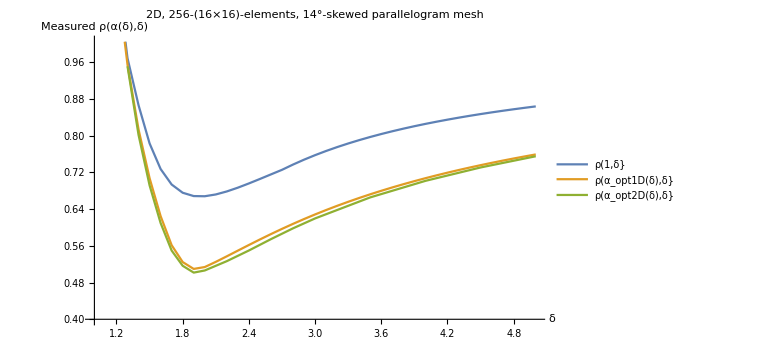

```mathematica
ListPlot[
{
{
{1.2,1.16309},{1.3,0.969073},{1.4,0.866645},{1.5,0.783438},{1.6,0.727569},{1.7,0.693772},{1.8,0.67584},{1.9,0.668584},{2,0.668194},{2.1,0.672095},{2.2,0.678666},{2.3,0.68689},{2.4,0.696114},{2.5,0.705871},{2.6,0.715848},{2.7,0.725789},{2.8,0.737272},{2.9,0.747928},{3,0.757783},{3.1,0.766903},{3.2,0.775354},{3.3,0.783223},{3.4,0.790568},{3.5,0.797428},{3.6,0.803842},{3.7,0.809867},{3.8,0.815529},{3.9,0.820878},{4,0.825921},{4.1,0.830652},{4.2,0.835156},{4.3,0.83943},{4.4,0.843483},{4.5,0.847335},{4.6,0.851001},{4.7,0.854494},{4.8,0.857826},{4.9,0.861008},{5,0.864054}
},
{
{1.2,1.1525},{1.3,0.955032},{1.4,0.813801},{1.5,0.707595},{1.6,0.624839},{1.7,0.561502},{1.8,0.524704},{1.9,0.509778},{2,0.51385},{2.1,0.525139},{2.2,0.53727},{2.3,0.54963},{2.4,0.561921},{2.5,0.573989},{2.6,0.585726},{2.7,0.597075},{2.8,0.608},{2.9,0.618482},{3,0.628533},{3.1,0.638131},{3.2,0.647313},{3.3,0.656071},{3.4,0.66445},{3.5,0.672455},{3.6,0.680094},{3.7,0.687411},{3.8,0.6944},{3.9,0.701103},{4,0.707515},{4.1,0.713674},{4.2,0.719579},{4.3,0.725244},{4.4,0.730695},{4.5,0.735931},{4.6,0.740968},{4.7,0.745819},{4.8,0.750496},{4.9,0.755004},{5,0.759351}
},
{
{1.3,0.951482},{1.4,0.801982},{1.5,0.691999},{1.6,0.609795},{1.7,0.549793},{1.8,0.516624},{1.9,0.501725},{2,0.506377},{2.2,0.526697},{2.4,0.54995},{2.6,0.574686},{2.8,0.598264},{3,0.619857},{3.5,0.665727},{4,0.701731},{4.5,0.730949},{5,0.755382}
}
},Joined->True,PlotRange->{{1,5},{0.4,1.005}},ImageSize->Large,AxesLabel->{"δ","Measured ρ(α(δ),δ)"},PlotLabel->"2D, 256-(16×16)-elements, 14°-skewed parallelogram mesh", PlotLegends->{"ρ(1,δ}","ρ(α_opt1D(δ),δ}","ρ(α_opt2D(δ),δ}"}]
```

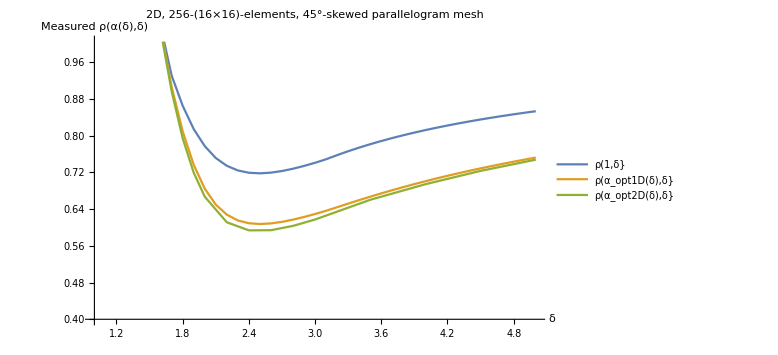

```mathematica
ListPlot[
{
{
{1.6,1.03925},{1.7,0.931396},{1.8,0.865388},{1.9,0.814659},{2,0.777444},{2.1,0.751527},{2.2,0.734571},{2.3,0.724451},{2.4,0.719429},{2.5,0.718146},{2.6,0.719651},{2.7,0.723197},{2.8,0.728187},{2.9,0.734289},{3,0.741148},{3.1,0.748848},{3.2,0.757861},{3.3,0.766341},{3.4,0.774264},{3.5,0.781668},{3.6,0.788601},{3.7,0.795111},{3.8,0.801226},{3.9,0.806983},{4,0.812417},{4.1,0.817545},{4.2,0.822407},{4.3,0.827012},{4.4,0.831384},{4.5,0.835537},{4.6,0.839486},{4.7,0.84326},{4.8,0.846843},{4.9,0.850273},{5,0.853558}
},
{
{1.6,1.03514},{1.7,0.906659},{1.8,0.809546},{1.9,0.736742},{2,0.684739},{2.1,0.649935},{2.2,0.628075},{2.3,0.615459},{2.4,0.609316},{2.5,0.607662},{2.6,0.608992},{2.7,0.612322},{2.8,0.617177},{2.9,0.623017},{3,0.629519},{3.1,0.636526},{3.2,0.644319},{3.3,0.652159},{3.4,0.659817},{3.5,0.667244},{3.6,0.674463},{3.7,0.681427},{3.8,0.688167},{3.9,0.694656},{4,0.700904},{4.1,0.70695},{4.2,0.712761},{4.3,0.718373},{4.4,0.723775},{4.5,0.728986},{4.6,0.734022},{4.7,0.738874},{4.8,0.743576},{4.9,0.748102},{5,0.752481}
},
{
{1.6,1.03},{1.7,0.897225},{1.8,0.794371},{1.9,0.719596},{2,0.667309},{2.2,0.611407},{2.4,0.593814},{2.6,0.594186},{2.8,0.603543},{3,0.617488},{3.5,0.660488},{4,0.694453},{4.5,0.723539},{5,0.747879}
}
},Joined->True,PlotRange->{{1,5},{0.4,1.005}},ImageSize->Large,AxesLabel->{"δ","Measured ρ(α(δ),δ)"},PlotLabel->"2D, 256-(16×16)-elements, 45°-skewed parallelogram mesh", PlotLegends->{"ρ(1,δ}","ρ(α_opt1D(δ),δ}","ρ(α_opt2D(δ),δ}"}]
```

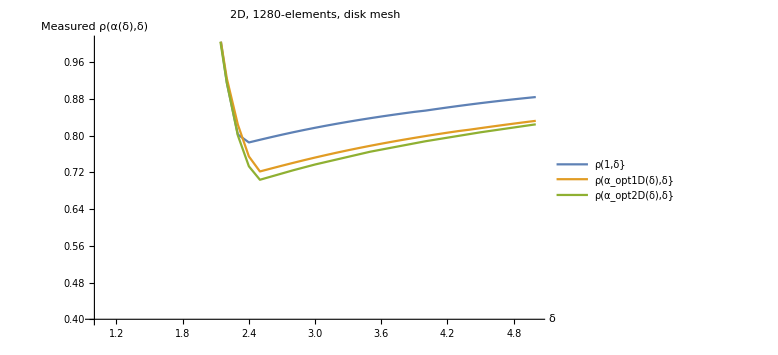

```mathematica
ListPlot[
{
{
{2.1,1.08289},{2.2,0.915756},{2.3,0.802817},{2.4,0.785467},{2.5,0.791254},{2.6,0.79691},{2.7,0.802385},{2.8,0.807631},{2.9,0.812649},{3,0.817445},{3.1,0.822021},{3.2,0.826384},{3.3,0.830552},{3.4,0.834546},{3.5,0.838357},{3.6,0.842016},{3.7,0.845509},{3.8,0.848872},{3.9,0.852114},{4,0.854871},{4.1,0.858353},{4.2,0.861733},{4.3,0.865002},{4.4,0.868145},{4.5,.871163},{4.6,0.874055},{4.7,0.876825},{4.8,0.879466},{4.9,0.882007},{5,0.884445}
},
{
{2.1,1.07369},{2.2,0.925036},{2.3,0.824379},{2.4,0.754992},{2.5,0.722224},{2.6,0.728542},{2.7,0.73479},{2.8,0.740893},{2.9,0.746824},{3,0.752559},{3.1,0.758074},{3.2,0.763403},{3.3,0.76852},{3.4,0.773449},{3.5,0.778191},{3.6,0.782747},{3.7,0.787138},{3.8,0.791365},{3.9,0.795417},{4,0.799352},{4.1,0.803132},{4.2,0.80678},{4.3,0.810296},{4.4,0.813301},{4.5,0.816705},{4.6,0.820043},{4.7,0.823302},{4.8,0.826473},{4.9,0.829568},{5,0.832594}
},
{
{2.1,1.07},{2.2,0.915756},{2.3,0.800851},{2.4,0.733466},{2.5,0.704132},{2.6,0.710985},{2.8,0.724729},{3,0.737428},{3.5,0.765302},{4,0.788067},{4.5,0.80764},{5,0.824986}
}
},Joined->True,PlotRange->{{1,5},{0.4,1.005}},ImageSize->Large,AxesLabel->{"δ","Measured ρ(α(δ),δ)"},PlotLabel->"2D, 1280-elements, disk mesh", PlotLegends->{"ρ(1,δ}","ρ(α_opt1D(δ),δ}","ρ(α_opt2D(δ),δ}"}]
```

```mathematica
ρ[δ_]=If[δ>Root[-1+4 #1-8 #1^2+4 #1^3&,1],1+(α[δ] (2+(-2-4δ)δ+√(4-24 δ+52 δ^2-48 δ^3+16 δ^4)))/(4 δ^2),1+(α[δ] (2-4 δ^2+√(4-32 δ+80 δ^2-64 δ^3+16 δ^4)))/(δ (-2+4 δ))];
```

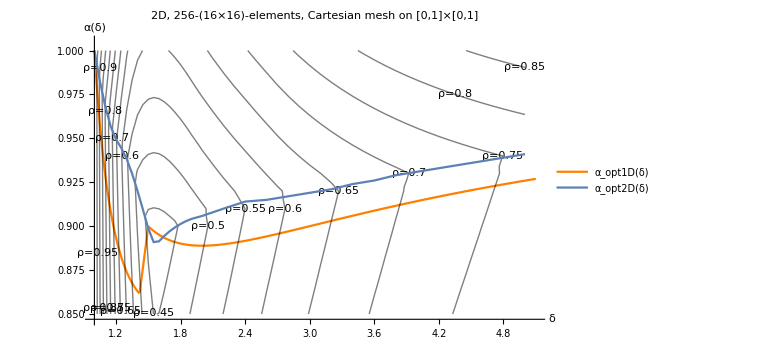

```mathematica
Show[
Plot[α[δ],{δ,1,5.1},PlotRange->{0.847,1.005},ImageSize->Large,AxesLabel->{"δ","α(δ)"},PlotStyle->Orange,PlotLegends->{"α_opt1D(δ)"},PlotLabel->"2D, 256-(16×16)-elements, Cartesian mesh on [0,1]×[0,1]"],
ListContourPlot[
{
{1,0.85,1},{1,0.86,1},{1,0.87,1},{1,0.88,1},{1,0.89,1},{1,0.9,1},{1,0.91,1},{1,0.92,1},{1,0.93,1},{1,0.94,1},{1,0.95,1},{1,0.96,1},{1,0.97,1},{1,0.98,1},{1,0.99,1},{1,1,1},{1.05,0.85,0.905108},{1.05,0.86,0.903976},{1.05,0.87,0.90285},{1.05,0.88,0.901692},{1.05,0.89,0.900559},{1.05,0.9,0.8994},{1.05,0.91,0.898281},{1.05,0.92,0.897154},{1.05,0.93,0.896036},{1.05,0.94,0.895164},{1.05,0.95,0.893799},{1.05,0.96,0.892675},{1.05,0.97,0.891731},{1.05,0.98,0.890485},{1.05,0.99,0.901324},{1.05,1,0.92053},{1.1,0.85,0.823246},{1.1,0.86,0.821178},{1.1,0.87,0.818848},{1.1,0.88,0.816761},{1.1,0.89,0.814929},{1.1,0.9,0.812836},{1.1,0.91,0.810555},{1.1,0.92,0.808422},{1.1,0.93,0.806598},{1.1,0.94,0.804479},{1.1,0.95,0.80233},{1.1,0.96,0.80019},{1.1,0.97,0.799864},{1.1,0.98,0.818415},{1.1,0.99,0.836972},{1.1,1,0.855529},{1.15,0.85,0.751075},{1.15,0.86,0.748147},{1.15,0.87,0.745217},{1.15,0.88,0.74233},{1.15,0.89,0.739384},{1.15,0.9,0.73649},{1.15,0.91,0.73358},{1.15,0.92,0.730637},{1.15,0.93,0.727721},{1.15,0.94,0.724781},{1.15,0.95,0.721881},{1.15,0.96,0.724981},{1.15,0.97,0.74295},{1.15,0.98,0.760921},{1.15,0.99,0.778888},{1.15,1,0.796856},{1.2,0.85,0.691676},{1.2,0.86,0.688076},{1.2,0.87,0.684425},{1.2,0.88,0.680786},{1.2,0.89,0.677157},{1.2,0.9,0.673535},{1.2,0.91,0.669919},{1.2,0.92,0.666299},{1.2,0.93,0.662662},{1.2,0.94,0.65907},{1.2,0.95,0.656508},{1.2,0.96,0.67395},{1.2,0.97,0.691382},{1.2,0.98,0.708831},{1.2,0.99,0.726256},{1.2,1,0.743696},{1.25,0.85,0.641664},{1.25,0.86,0.637447},{1.25,0.87,0.633216},{1.25,0.88,0.628999},{1.25,0.89,0.624788},{1.25,0.9,0.620577},{1.25,0.91,0.616352},{1.25,0.92,0.612137},{1.25,0.93,0.607952},{1.25,0.94,0.603734},{1.25,0.95,0.611046},{1.25,0.96,0.628005},{1.25,0.97,0.644962},{1.25,0.98,0.661921},{1.25,0.99,0.678879},{1.25,1,0.695837},{1.3,0.85,0.597995},{1.3,0.86,0.593265},{1.3,0.87,0.588537},{1.3,0.88,0.583808},{1.3,0.89,0.579079},{1.3,0.9,0.574347},{1.3,0.91,0.569619},{1.3,0.92,0.564886},{1.3,0.93,0.560173},{1.3,0.94,0.556177},{1.3,0.95,0.57274},{1.3,0.96,0.589288},{1.3,0.97,0.605841},{1.3,0.98,0.622397},{1.3,0.99,0.638953},{1.3,1,0.655508},{1.35,0.85,0.55959},{1.35,0.86,0.554409},{1.35,0.87,0.549228},{1.35,0.88,0.544049},{1.35,0.89,0.538866},{1.35,0.9,0.533684},{1.35,0.91,0.528505},{1.35,0.92,0.523333},{1.35,0.93,0.518152},{1.35,0.94,0.529696},{1.35,0.95,0.545971},{1.35,0.96,0.562235},{1.35,0.97,0.578508},{1.35,0.98,0.594787},{1.35,0.99,0.611056},{1.35,1,0.627337},{1.4,0.85,0.525586},{1.4,0.86,0.520005},{1.4,0.87,0.514424},{1.4,0.88,0.508841},{1.4,0.89,0.503264},{1.4,0.9,0.497688},{1.4,0.91,0.492106},{1.4,0.92,0.486525},{1.4,0.93,0.496461},{1.4,0.94,0.512557},{1.4,0.95,0.528644},{1.4,0.96,0.544734},{1.4,0.97,0.56082},{1.4,0.98,0.576914},{1.4,0.99,0.593008},{1.4,1,0.6091},{1.45,0.85,0.495346},{1.45,0.86,0.489409},{1.45,0.87,0.483472},{1.45,0.88,0.477535},{1.45,0.89,0.471603},{1.45,0.9,0.465666},{1.45,0.91,0.459728},{1.45,0.92,0.471389},{1.45,0.93,0.48738},{1.45,0.94,0.503371},{1.45,0.95,0.519366},{1.45,0.96,0.53536},{1.45,0.97,0.551351},{1.45,0.98,0.567346},{1.45,0.99,0.583339},{1.45,1,0.599334},{1.5,0.85,0.46853},{1.5,0.86,0.46228},{1.5,0.87,0.456026},{1.5,0.88,0.449775},{1.5,0.89,0.443523},{1.5,0.9,0.43727},{1.5,0.91,0.45075},{1.5,0.92,0.466699},{1.5,0.93,0.482637},{1.5,0.94,0.49858},{1.5,0.95,0.514523},{1.5,0.96,0.530465},{1.5,0.97,0.546407},{1.5,0.98,0.562349},{1.5,0.99,0.57829},{1.5,1,0.594234},{1.55,0.85,0.44947},{1.55,0.86,0.44299},{1.55,0.87,0.436514},{1.55,0.88,0.430038},{1.55,0.89,0.42356},{1.55,0.9,0.433339},{1.55,0.91,0.449266},{1.55,0.92,0.465193},{1.55,0.93,0.481117},{1.55,0.94,0.497043},{1.55,0.95,0.512968},{1.55,0.96,0.528894},{1.55,0.97,0.544821},{1.55,0.98,0.560745},{1.55,0.99,0.57667},{1.55,1,0.592597},{1.6,0.85,0.450367},{1.6,0.86,0.443895},{1.6,0.87,0.437432},{1.6,0.88,0.430965},{1.6,0.89,0.424498},{1.6,0.9,0.434254},{1.6,0.91,0.45019},{1.6,0.92,0.466129},{1.6,0.93,0.482065},{1.6,0.94,0.497999},{1.6,0.95,0.513937},{1.6,0.96,0.529875},{1.6,0.97,0.54581},{1.6,0.98,0.561745},{1.6,0.99,0.57768},{1.6,1,0.593616},{1.65,0.85,0.458575},{1.65,0.86,0.452207},{1.65,0.87,0.445839},{1.65,0.88,0.439468},{1.65,0.89,0.433098},{1.65,0.9,0.436978},{1.65,0.91,0.452947},{1.65,0.92,0.46892},{1.65,0.93,0.484878},{1.65,0.94,0.500845},{1.65,0.95,0.516811},{1.65,0.96,0.532781},{1.65,0.97,0.548746},{1.65,0.98,0.564708},{1.65,0.99,0.580681},{1.65,1,0.596645},{1.7,0.85,0.467276},{1.7,0.86,0.461008},{1.7,0.87,0.454742},{1.7,0.88,0.448472},{1.7,0.89,0.442204},{1.7,0.9,0.44103},{1.7,0.91,0.457042},{1.7,0.92,0.473059},{1.7,0.93,0.489063},{1.7,0.94,0.505073},{1.7,0.95,0.521084},{1.7,0.96,0.537092},{1.7,0.97,0.553096},{1.7,0.98,0.569108},{1.7,0.99,0.585125},{1.7,1,0.601137},{1.75,0.85,0.476089},{1.75,0.86,0.469925},{1.75,0.87,0.463761},{1.75,0.88,0.457598},{1.75,0.89,0.451434},{1.75,0.9,0.445269},{1.75,0.91,0.46207},{1.75,0.92,0.478158},{1.75,0.93,0.494224},{1.75,0.94,0.51029},{1.75,0.95,0.526356},{1.75,0.96,0.54242},{1.75,0.97,0.558482},{1.75,0.98,0.574553},{1.75,0.99,0.590606},{1.75,1,0.606677},{1.8,0.85,0.484895},{1.8,0.86,0.478835},{1.8,0.87,0.472776},{1.8,0.88,0.466714},{1.8,0.89,0.460653},{1.8,0.9,0.454592},{1.8,0.91,0.467746},{1.8,0.92,0.483942},{1.8,0.93,0.500054},{1.8,0.94,0.516174},{1.8,0.95,0.532297},{1.8,0.96,0.548436},{1.8,0.97,0.564572},{1.8,0.98,0.580685},{1.8,0.99,0.596815},{1.8,1,0.612949},{1.85,0.85,0.493632},{1.85,0.86,0.487674},{1.85,0.87,0.481717},{1.85,0.88,0.475761},{1.85,0.89,0.469801},{1.85,0.9,0.463843},{1.85,0.91,0.474145},{1.85,0.92,0.490387},{1.85,0.93,0.506607},{1.85,0.94,0.522781},{1.85,0.95,0.538997},{1.85,0.96,0.55519},{1.85,0.97,0.571329},{1.85,0.98,0.587574},{1.85,0.99,0.603808},{1.85,1,0.620025},{1.9,0.85,0.502257},{1.9,0.86,0.496401},{1.9,0.87,0.490545},{1.9,0.88,0.484689},{1.9,0.89,0.478829},{1.9,0.9,0.472972},{1.9,0.91,0.481194},{1.9,0.92,0.497533},{1.9,0.93,0.513827},{1.9,0.94,0.530107},{1.9,0.95,0.546408},{1.9,0.96,0.562707},{1.9,0.97,0.57889},{1.9,0.98,0.595205},{1.9,0.99,0.611512},{1.9,1,0.627803},{1.95,0.85,0.510745},{1.95,0.86,0.504988},{1.95,0.87,0.499233},{1.95,0.88,0.493477},{1.95,0.89,0.48772},{1.95,0.9,0.481964},{1.95,0.91,0.488242},{1.95,0.92,0.504396},{1.95,0.93,0.521031},{1.95,0.94,0.537437},{1.95,0.95,0.553431},{1.95,0.96,0.569814},{1.95,0.97,0.58645},{1.95,0.98,0.602835},{1.95,0.99,0.61921},{1.95,1,0.635607},{2,0.85,0.519081},{2,0.86,0.513423},{2,0.87,0.507765},{2,0.88,0.502107},{2,0.89,0.49645},{2,0.9,0.490792},{2,0.91,0.495057},{2,0.92,0.511386},{2,0.93,0.52783},{2,0.94,0.544492},{2,0.95,0.561028},{2,0.96,0.577363},{2,0.97,0.593858},{2,0.98,0.610305},{2,0.99,0.626373},{2,1,0.64277},{2.1,0.85,0.535261},{2.1,0.86,0.529794},{2.1,0.87,0.524327},{2.1,0.88,0.518859},{2.1,0.89,0.513391},{2.1,0.9,0.507925},{2.1,0.91,0.508372},{2.1,0.92,0.524931},{2.1,0.93,0.541496},{2.1,0.94,0.558047},{2.1,0.95,0.574695},{2.1,0.96,0.591207},{2.1,0.97,0.607785},{2.1,0.98,0.624349},{2.1,0.99,0.640925},{2.1,1,0.657486},{2.2,0.85,0.550765},{2.2,0.86,0.54548},{2.2,0.87,0.540194},{2.2,0.88,0.534909},{2.2,0.89,0.529624},{2.2,0.9,0.524339},{2.2,0.91,0.519054},{2.2,0.92,0.537662},{2.2,0.93,0.554411},{2.2,0.94,0.571139},{2.2,0.95,0.587777},{2.2,0.96,0.604505},{2.2,0.97,0.621267},{2.2,0.98,0.637939},{2.2,0.99,0.654673},{2.2,1,0.671373},{2.3,0.85,0.565581},{2.3,0.86,0.56047},{2.3,0.87,0.555361},{2.3,0.88,0.550251},{2.3,0.89,0.54514},{2.3,0.9,0.540023},{2.3,0.91,0.534912},{2.3,0.92,0.549734},{2.3,0.93,0.566592},{2.3,0.94,0.58343},{2.3,0.95,0.600275},{2.3,0.96,0.617117},{2.3,0.97,0.633961},{2.3,0.98,0.650809},{2.3,0.99,0.667666},{2.3,1,0.684532},{2.4,0.85,0.579719},{2.4,0.86,0.574774},{2.4,0.87,0.56983},{2.4,0.88,0.564886},{2.4,0.89,0.559941},{2.4,0.9,0.554997},{2.4,0.91,0.550053},{2.4,0.92,0.561149},{2.4,0.93,0.578146},{2.4,0.94,0.595093},{2.4,0.95,0.612049},{2.4,0.96,0.629012},{2.4,0.97,0.645976},{2.4,0.98,0.662935},{2.4,0.99,0.679941},{2.4,1,0.696899},{2.5,0.85,0.593195},{2.5,0.86,0.588407},{2.5,0.87,0.583621},{2.5,0.88,0.578835},{2.5,0.89,0.574049},{2.5,0.9,0.569266},{2.5,0.91,0.56448},{2.5,0.92,0.572102},{2.5,0.93,0.589856},{2.5,0.94,0.606933},{2.5,0.95,0.624034},{2.5,0.96,0.641168},{2.5,0.97,0.658217},{2.5,0.98,0.675266},{2.5,0.99,0.692444},{2.5,1,0.709524},{2.6,0.85,0.606017},{2.6,0.86,0.601382},{2.6,0.87,0.596747},{2.6,0.88,0.592112},{2.6,0.89,0.587477},{2.6,0.9,0.582843},{2.6,0.91,0.578208},{2.6,0.92,0.584075},{2.6,0.93,0.601291},{2.6,0.94,0.618502},{2.6,0.95,0.63571},{2.6,0.96,0.652922},{2.6,0.97,0.670135},{2.6,0.98,0.687351},{2.6,0.99,0.704567},{2.6,1,0.721791},{2.7,0.85,0.61821},{2.7,0.86,0.613712},{2.7,0.87,0.60922},{2.7,0.88,0.604729},{2.7,0.89,0.600237},{2.7,0.9,0.595746},{2.7,0.91,0.591255},{2.7,0.92,0.595312},{2.7,0.93,0.612652},{2.7,0.94,0.629987},{2.7,0.95,0.647321},{2.7,0.96,0.664656},{2.7,0.97,0.681994},{2.7,0.98,0.69934},{2.7,0.99,0.716681},{2.7,1,0.734061},{2.8,0.85,0.629783},{2.8,0.86,0.625431},{2.8,0.87,0.621067},{2.8,0.88,0.616712},{2.8,0.89,0.612357},{2.8,0.9,0.608002},{2.8,0.91,0.603646},{2.8,0.92,0.605644},{2.8,0.93,0.623097},{2.8,0.94,0.640545},{2.8,0.95,0.657993},{2.8,0.96,0.6755},{2.8,0.97,0.692893},{2.8,0.98,0.710347},{2.8,0.99,0.727803},{2.8,1,0.745258},{2.9,0.85,0.64077},{2.9,0.86,0.636545},{2.9,0.87,0.632322},{2.9,0.88,0.628088},{2.9,0.89,0.623862},{2.9,0.9,0.619636},{2.9,0.91,0.61541},{2.9,0.92,0.615149},{2.9,0.93,0.632705},{2.9,0.94,0.650259},{2.9,0.95,0.667845},{2.9,0.96,0.685405},{2.9,0.97,0.702963},{2.9,0.98,0.720468},{2.9,0.99,0.738027},{2.9,1,0.755602},{3,0.85,0.651197},{3,0.86,0.647095},{3,0.87,0.642994},{3,0.88,0.638891},{3,0.89,0.634778},{3,0.9,0.630674},{3,0.91,0.626571},{3,0.92,0.623916},{3,0.93,0.641569},{3,0.94,0.659213},{3,0.95,0.67689},{3,0.96,0.694544},{3,0.97,0.712198},{3,0.98,0.729851},{3,0.99,0.747457},{3,1,0.76512},{3.1,0.85,0.661093},{3.1,0.86,0.657109},{3.1,0.87,0.65312},{3.1,0.88,0.649138},{3.1,0.89,0.645143},{3.1,0.9,0.641156},{3.1,0.91,0.637169},{3.1,0.92,0.633182},{3.1,0.93,0.649768},{3.1,0.94,0.667502},{3.1,0.95,0.685263},{3.1,0.96,0.703003},{3.1,0.97,0.720742},{3.1,0.98,0.738486},{3.1,0.99,0.756225},{3.1,1,0.773933},{3.2,0.85,0.670489},{3.2,0.86,0.666617},{3.2,0.87,0.662741},{3.2,0.88,0.658866},{3.2,0.89,0.654991},{3.2,0.9,0.651103},{3.2,0.91,0.647227},{3.2,0.92,0.64335},{3.2,0.93,0.657374},{3.2,0.94,0.675192},{3.2,0.95,0.693029},{3.2,0.96,0.710849},{3.2,0.97,0.728673},{3.2,0.98,0.74649},{3.2,0.99,0.764295},{3.2,1,0.782109},{3.3,0.85,0.679421},{3.3,0.86,0.675649},{3.3,0.87,0.671878},{3.3,0.88,0.668108},{3.3,0.89,0.664339},{3.3,0.9,0.660559},{3.3,0.91,0.656788},{3.3,0.92,0.653016},{3.3,0.93,0.664449},{3.3,0.94,0.68235},{3.3,0.95,0.700257},{3.3,0.96,0.718155},{3.3,0.97,0.736053},{3.3,0.98,0.753949},{3.3,0.99,0.77185},{3.3,1,0.789712},{3.4,0.85,0.687907},{3.4,0.86,0.684231},{3.4,0.87,0.68056},{3.4,0.88,0.676888},{3.4,0.89,0.673225},{3.4,0.9,0.66954},{3.4,0.91,0.665869},{3.4,0.92,0.662196},{3.4,0.93,0.671053},{3.4,0.94,0.689018},{3.4,0.95,0.707},{3.4,0.96,0.724965},{3.4,0.97,0.742933},{3.4,0.98,0.760898},{3.4,0.99,0.778867},{3.4,1,0.796797},{3.5,0.85,0.69598},{3.5,0.86,0.692405},{3.5,0.87,0.688823},{3.5,0.88,0.685251},{3.5,0.89,0.681677},{3.5,0.9,0.678092},{3.5,0.91,0.674515},{3.5,0.92,0.670938},{3.5,0.93,0.677218},{3.5,0.94,0.695256},{3.5,0.95,0.713301},{3.5,0.96,0.731338},{3.5,0.97,0.749367},{3.5,0.98,0.767396},{3.5,0.99,0.78543},{3.5,1,0.803434},{3.6,0.85,0.703666},{3.6,0.86,0.700181},{3.6,0.87,0.696695},{3.6,0.88,0.69321},{3.6,0.89,0.689723},{3.6,0.9,0.68624},{3.6,0.91,0.682747},{3.6,0.92,0.67926},{3.6,0.93,0.682999},{3.6,0.94,0.701092},{3.6,0.95,0.719204},{3.6,0.96,0.737291},{3.6,0.97,0.755393},{3.6,0.98,0.773483},{3.6,0.99,0.791579},{3.6,1,0.809649},{3.7,0.85,0.710989},{3.7,0.86,0.707591},{3.7,0.87,0.70419},{3.7,0.88,0.700788},{3.7,0.89,0.697392},{3.7,0.9,0.693996},{3.7,0.91,0.690581},{3.7,0.92,0.68718},{3.7,0.93,0.688424},{3.7,0.94,0.706576},{3.7,0.95,0.724745},{3.7,0.96,0.742909},{3.7,0.97,0.761057},{3.7,0.98,0.779203},{3.7,0.99,0.79735},{3.7,1,0.815482},{3.8,0.85,0.717973},{3.8,0.86,0.714657},{3.8,0.87,0.711338},{3.8,0.88,0.708018},{3.8,0.89,0.704702},{3.8,0.9,0.701391},{3.8,0.91,0.698062},{3.8,0.92,0.694743},{3.8,0.93,0.693518},{3.8,0.94,0.711724},{3.8,0.95,0.729957},{3.8,0.96,0.748132},{3.8,0.97,0.766369},{3.8,0.98,0.784575},{3.8,0.99,0.802775},{3.8,1,0.820967},{3.9,0.85,0.724639},{3.9,0.86,0.721402},{3.9,0.87,0.718165},{3.9,0.88,0.714919},{3.9,0.89,0.711687},{3.9,0.9,0.708448},{3.9,0.91,0.705201},{3.9,0.92,0.701961},{3.9,0.93,0.698721},{3.9,0.94,0.716583},{3.9,0.95,0.73488},{3.9,0.96,0.753097},{3.9,0.97,0.771345},{3.9,0.98,0.789631},{3.9,0.99,0.807894},{3.9,1,0.826134},{4,0.85,0.731013},{4,0.86,0.727845},{4,0.87,0.724684},{4,0.88,0.72152},{4,0.89,0.718356},{4,0.9,0.715191},{4,0.91,0.712021},{4,0.92,0.708856},{4,0.93,0.705691},{4,0.94,0.721168},{4,0.95,0.739509},{4,0.96,0.757785},{4,0.97,0.776084},{4,0.98,0.794381},{4,0.99,0.812709},{4,1,0.83101},{4.1,0.85,0.737102},{4.1,0.86,0.734005},{4.1,0.87,0.730916},{4.1,0.88,0.72782},{4.1,0.89,0.724732},{4.1,0.9,0.721639},{4.1,0.91,0.718551},{4.1,0.92,0.715449},{4.1,0.93,0.712355},{4.1,0.94,0.725501},{4.1,0.95,0.743886},{4.1,0.96,0.762216},{4.1,0.97,0.780563},{4.1,0.98,0.798907},{4.1,0.99,0.817276},{4.1,1,0.835618},{4.2,0.85,0.742929},{4.2,0.86,0.739906},{4.2,0.87,0.73688},{4.2,0.88,0.733857},{4.2,0.89,0.730825},{4.2,0.9,0.72781},{4.2,0.91,0.724789},{4.2,0.92,0.721757},{4.2,0.93,0.718732},{4.2,0.94,0.729604},{4.2,0.95,0.748029},{4.2,0.96,0.766429},{4.2,0.97,0.784801},{4.2,0.98,0.803191},{4.2,0.99,0.821601},{4.2,1,0.839981},{4.3,0.85,0.748509},{4.3,0.86,0.745552},{4.3,0.87,0.742592},{4.3,0.88,0.739634},{4.3,0.89,0.736678},{4.3,0.9,0.733712},{4.3,0.91,0.730763},{4.3,0.92,0.727798},{4.3,0.93,0.724839},{4.3,0.94,0.733493},{4.3,0.95,0.75193},{4.3,0.96,0.770399},{4.3,0.97,0.788818},{4.3,0.98,0.807253},{4.3,0.99,0.825702},{4.3,1,0.844117},{4.4,0.85,0.753857},{4.4,0.86,0.750964},{4.4,0.87,0.748066},{4.4,0.88,0.745171},{4.4,0.89,0.742278},{4.4,0.9,0.739375},{4.4,0.91,0.73649},{4.4,0.92,0.733588},{4.4,0.93,0.730692},{4.4,0.94,0.737172},{4.4,0.95,0.755649},{4.4,0.96,0.77417},{4.4,0.97,0.792632},{4.4,0.98,0.811108},{4.4,0.99,0.829578},{4.4,1,0.848045},{4.5,0.85,0.758987},{4.5,0.86,0.756154},{4.5,0.87,0.753317},{4.5,0.88,0.750482},{4.5,0.89,0.747649},{4.5,0.9,0.744806},{4.5,0.91,0.741984},{4.5,0.92,0.739143},{4.5,0.93,0.736306},{4.5,0.94,0.740682},{4.5,0.95,0.759196},{4.5,0.96,0.777755},{4.5,0.97,0.796258},{4.5,0.98,0.814773},{4.5,0.99,0.833282},{4.5,1,0.851778},{4.6,0.85,0.763918},{4.6,0.86,0.761137},{4.6,0.87,0.758363},{4.6,0.88,0.755585},{4.6,0.89,0.752805},{4.6,0.9,0.750033},{4.6,0.91,0.74725},{4.6,0.92,0.744474},{4.6,0.93,0.741696},{4.6,0.94,0.744023},{4.6,0.95,0.762573},{4.6,0.96,0.781167},{4.6,0.97,0.799709},{4.6,0.98,0.818259},{4.6,0.99,0.836804},{4.6,1,0.855333},{4.7,0.85,0.76865},{4.7,0.86,0.765923},{4.7,0.87,0.763206},{4.7,0.88,0.760483},{4.7,0.89,0.757756},{4.7,0.9,0.755043},{4.7,0.91,0.752316},{4.7,0.92,0.749596},{4.7,0.93,0.746873},{4.7,0.94,0.747206},{4.7,0.95,0.76579},{4.7,0.96,0.784419},{4.7,0.97,0.803002},{4.7,0.98,0.82158},{4.7,0.99,0.840163},{4.7,1,0.85872},{4.8,0.85,0.773198},{4.8,0.86,0.770525},{4.8,0.87,0.76786},{4.8,0.88,0.765192},{4.8,0.89,0.76252},{4.8,0.9,0.759849},{4.8,0.91,0.757185},{4.8,0.92,0.754529},{4.8,0.93,0.75185},{4.8,0.94,0.750243},{4.8,0.95,0.768859},{4.8,0.96,0.787521},{4.8,0.97,0.806137},{4.8,0.98,0.824748},{4.8,0.99,0.843363},{4.8,1,0.861953},{4.9,0.85,0.777574},{4.9,0.86,0.77496},{4.9,0.87,0.772338},{4.9,0.88,0.769722},{4.9,0.89,0.767108},{4.9,0.9,0.764493},{4.9,0.91,0.761869},{4.9,0.92,0.759266},{4.9,0.93,0.756638},{4.9,0.94,0.75402},{4.9,0.95,0.771791},{4.9,0.96,0.790485},{4.9,0.97,0.80913},{4.9,0.98,0.827773},{4.9,0.99,0.846418},{4.9,1,0.86504},{5,0.85,0.781787},{5,0.86,0.779222},{5,0.87,0.77665},{5,0.88,0.774088},{5,0.89,0.771518},{5,0.9,0.768952},{5,0.91,0.766381},{5,0.92,0.763825},{5,0.93,0.761248},{5,0.94,0.758679},{5,0.95,0.774594},{5,0.96,0.793317},{5,0.97,0.811991},{5,0.98,0.830664},{5,0.99,0.849339},{5,1,0.867993}
}
,Contours->{0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1},ContourShading->None,ContourLabels->(Text[StringJoin["ρ=",ToString[#3]],{#1,#2}]&)],
ListPlot[
{
{1.0,1},{1.05,0.9828125000000002},{1.1,0.9684936523437502},{1.15,0.95703125},{1.2,0.94945068359375},{1.25,0.9444885253906249},{1.3,0.93819580078125},{1.35,0.9299194335937497},{1.4,0.9201416015625001},{1.45,0.9096008300781249},{1.5,0.8988098144531249},{1.55,0.8909301757812499},{1.6,0.8913818359374999},{1.65,0.89451904296875},{1.7,0.8971618652343748},{1.75,0.8993713378906251},{1.8,0.9012451171875},{1.85,0.9028503417968748},{1.9,0.9041015625},{1.95,0.9049621582031249},{2.0,0.9058105468749997},{2.2,0.91},{2.4,0.914},{2.6,0.915},{2.8,0.917},{3,0.919},{3.2,0.921},{3.4,0.924},{3.6,0.926},{3.8,0.929},{4,0.931},{4.2,0.933},{4.4,0.935},{4.6,0.937},{4.8,0.939},{5,0.941}
},PlotStyle->PointSize[0.005],Joined->True,PlotLegends->{"α_opt2D(δ)"}
]
]
```

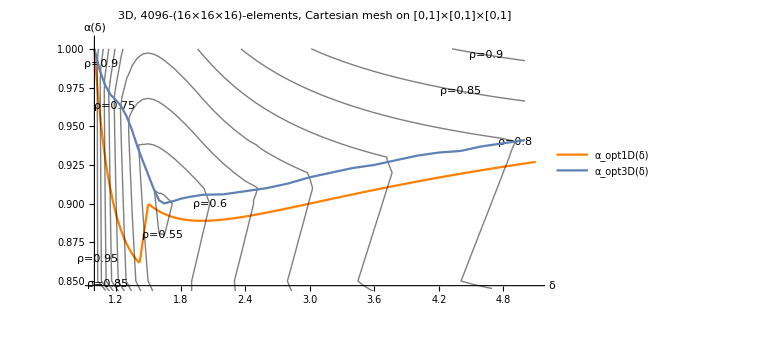

```mathematica
Show[
Plot[α[δ],{δ,1,5.1},PlotRange->{0.847,1.005},ImageSize->Large,AxesLabel->{"δ","α(δ)"},PlotStyle->Orange,PlotLegends->{"α_opt1D(δ)"},PlotLabel->"3D, 4096-(16×16×16)-elements, Cartesian mesh on [0,1]×[0,1]×[0,1]"],
ListContourPlot[
{
{1,0.85,1},{1,0.86,1},{1,0.87,1},{1,0.88,1},{1,0.89,1},{1,0.9,1},{1,0.91,1},{1,0.92,1},{1,0.93,1},{1,0.94,1},{1,0.95,1},{1,0.96,1},{1,0.97,1},{1,0.98,1},{1,0.99,1},{1,1,1},{1.05,0.85,0.917959},{1.05,0.86,0.916999},{1.05,0.87,0.916022},{1.05,0.88,0.915067},{1.05,0.89,0.914102},{1.05,0.9,0.913133},{1.05,0.91,0.912168},{1.05,0.92,0.911203},{1.05,0.93,0.910237},{1.05,0.94,0.909271},{1.05,0.95,0.908309},{1.05,0.96,0.907347},{1.05,0.97,0.906385},{1.05,0.98,0.905422},{1.05,0.99,0.914153},{1.05,1,0.933488},{1.1,0.85,0.858688},{1.1,0.86,0.857025},{1.1,0.87,0.855358},{1.1,0.88,0.85369},{1.1,0.89,0.852032},{1.1,0.9,0.850365},{1.1,0.91,0.848702},{1.1,0.92,0.84704},{1.1,0.93,0.845378},{1.1,0.94,0.843716},{1.1,0.95,0.842049},{1.1,0.96,0.840388},{1.1,0.97,0.838726},{1.1,0.98,0.843941},{1.1,0.99,0.862756},{1.1,1,0.881572},{1.15,0.85,0.808559},{1.15,0.86,0.806306},{1.15,0.87,0.804047},{1.15,0.88,0.801801},{1.15,0.89,0.799549},{1.15,0.9,0.797296},{1.15,0.91,0.795044},{1.15,0.92,0.792792},{1.15,0.93,0.79054},{1.15,0.94,0.788287},{1.15,0.95,0.786035},{1.15,0.96,0.783783},{1.15,0.97,0.781531},{1.15,0.98,0.79805},{1.15,0.99,0.816398},{1.15,1,0.834745},{1.2,0.85,0.765671},{1.2,0.86,0.762913},{1.2,0.87,0.760154},{1.2,0.88,0.757397},{1.2,0.89,0.75464},{1.2,0.9,0.751887},{1.2,0.91,0.74913},{1.2,0.92,0.746373},{1.2,0.93,0.743616},{1.2,0.94,0.74086},{1.2,0.95,0.738103},{1.2,0.96,0.735346},{1.2,0.97,0.738964},{1.2,0.98,0.756891},{1.2,0.99,0.774818},{1.2,1,0.792746},{1.25,0.85,0.728567},{1.25,0.86,0.725374},{1.25,0.87,0.72217},{1.25,0.88,0.718983},{1.25,0.89,0.715788},{1.25,0.9,0.712595},{1.25,0.91,0.709402},{1.25,0.92,0.706208},{1.25,0.93,0.703015},{1.25,0.94,0.699825},{1.25,0.95,0.696631},{1.25,0.96,0.693438},{1.25,0.97,0.705094},{1.25,0.98,0.722674},{1.25,0.99,0.74025},{1.25,1,0.757827},{1.3,0.85,0.696157},{1.3,0.86,0.692577},{1.3,0.87,0.689002},{1.3,0.88,0.685432},{1.3,0.89,0.681864},{1.3,0.9,0.678276},{1.3,0.91,0.674702},{1.3,0.92,0.671127},{1.3,0.93,0.667553},{1.3,0.94,0.663978},{1.3,0.95,0.660403},{1.3,0.96,0.663739},{1.3,0.97,0.681069},{1.3,0.98,0.698402},{1.3,0.99,0.715735},{1.3,1,0.733068},{1.35,0.85,0.667606},{1.35,0.86,0.663692},{1.35,0.87,0.659783},{1.35,0.88,0.655879},{1.35,0.89,0.651965},{1.35,0.9,0.648056},{1.35,0.91,0.644135},{1.35,0.92,0.640225},{1.35,0.93,0.636315},{1.35,0.94,0.632403},{1.35,0.95,0.632673},{1.35,0.96,0.649854},{1.35,0.97,0.66704},{1.35,0.98,0.685785},{1.35,0.99,0.701498},{1.35,1,0.718682},{1.4,0.85,0.642287},{1.4,0.86,0.638072},{1.4,0.87,0.633875},{1.4,0.88,0.629668},{1.4,0.89,0.625454},{1.4,0.9,0.621241},{1.4,0.91,0.617042},{1.4,0.92,0.612814},{1.4,0.93,0.608614},{1.4,0.94,0.604403},{1.4,0.95,0.624279},{1.4,0.96,0.641471},{1.4,0.97,0.65862},{1.4,0.98,0.675755},{1.4,0.99,0.692875},{1.4,1,0.70998},{1.45,0.85,0.619689},{1.45,0.86,0.615223},{1.45,0.87,0.610753},{1.45,0.88,0.60628},{1.45,0.89,0.601801},{1.45,0.9,0.59733},{1.45,0.91,0.592865},{1.45,0.92,0.588367},{1.45,0.93,0.583891},{1.45,0.94,0.603205},{1.45,0.95,0.620298},{1.45,0.96,0.637464},{1.45,0.97,0.654507},{1.45,0.98,0.671544},{1.45,0.99,0.688584},{1.45,1,0.705645},{1.5,0.85,0.59945},{1.5,0.86,0.594742},{1.5,0.87,0.590034},{1.5,0.88,0.585317},{1.5,0.89,0.580596},{1.5,0.9,0.575887},{1.5,0.91,0.571158},{1.5,0.92,0.566444},{1.5,0.93,0.585202},{1.5,0.94,0.602351},{1.5,0.95,0.619367},{1.5,0.96,0.636398},{1.5,0.97,0.65343},{1.5,0.98,0.670477},{1.5,0.99,0.687538},{1.5,1,0.704558},{1.55,0.85,0.581276},{1.55,0.86,0.57635},{1.55,0.87,0.571418},{1.55,0.88,0.566488},{1.55,0.89,0.561566},{1.55,0.9,0.556609},{1.55,0.91,0.551684},{1.55,0.92,0.569375},{1.55,0.93,0.586479},{1.55,0.94,0.603529},{1.55,0.95,0.62058},{1.55,0.96,0.637628},{1.55,0.97,0.65469},{1.55,0.98,0.671724},{1.55,0.99,0.68878},{1.55,1,0.705808},{1.6,0.85,0.565792},{1.6,0.86,0.560689},{1.6,0.87,0.555582},{1.6,0.88,0.55047},{1.6,0.89,0.54537},{1.6,0.9,0.540235},{1.6,0.91,0.555031},{1.6,0.92,0.572084},{1.6,0.93,0.589179},{1.6,0.94,0.606267},{1.6,0.95,0.623357},{1.6,0.96,0.640457},{1.6,0.97,0.657491},{1.6,0.98,0.674612},{1.6,0.99,0.691658},{1.6,1,0.708741},{1.65,0.85,0.565179},{1.65,0.86,0.560067},{1.65,0.87,0.554952},{1.65,0.88,0.549835},{1.65,0.89,0.544703},{1.65,0.9,0.539587},{1.65,0.91,0.558716},{1.65,0.92,0.575831},{1.65,0.93,0.592966},{1.65,0.94,0.610084},{1.65,0.95,0.627214},{1.65,0.96,0.64434},{1.65,0.97,0.661448},{1.65,0.98,0.67862},{1.65,0.99,0.695717},{1.65,1,0.712838},{1.7,0.85,0.571811},{1.7,0.86,0.566772},{1.7,0.87,0.561728},{1.7,0.88,0.556706},{1.7,0.89,0.551647},{1.7,0.9,0.546609},{1.7,0.91,0.563183},{1.7,0.92,0.580307},{1.7,0.93,0.59747},{1.7,0.94,0.614647},{1.7,0.95,0.631795},{1.7,0.96,0.648966},{1.7,0.97,0.666189},{1.7,0.98,0.683388},{1.7,0.99,0.700551},{1.7,1,0.717714},{1.75,0.85,0.578739},{1.75,0.86,0.573792},{1.75,0.87,0.568828},{1.75,0.88,0.563881},{1.75,0.89,0.558906},{1.75,0.9,0.55395},{1.75,0.91,0.567946},{1.75,0.92,0.585229},{1.75,0.93,0.602419},{1.75,0.94,0.619621},{1.75,0.95,0.636838},{1.75,0.96,0.654046},{1.75,0.97,0.671427},{1.75,0.98,0.688603},{1.75,0.99,0.705782},{1.75,1,0.722975},{1.8,0.85,0.585721},{1.8,0.86,0.580858},{1.8,0.87,0.575973},{1.8,0.88,0.57111},{1.8,0.89,0.566216},{1.8,0.9,0.561344},{1.8,0.91,0.573039},{1.8,0.92,0.590721},{1.8,0.93,0.608008},{1.8,0.94,0.625297},{1.8,0.95,0.642573},{1.8,0.96,0.659842},{1.8,0.97,0.677255},{1.8,0.98,0.694538},{1.8,0.99,0.711748},{1.8,1,0.729015},{1.85,0.8,0.592676},{1.85,0.86,0.587897},{1.85,0.87,0.583109},{1.85,0.88,0.578301},{1.85,0.89,0.573496},{1.85,0.9,0.568693},{1.85,0.91,0.578928},{1.85,0.92,0.596356},{1.85,0.93,0.613705},{1.85,0.94,0.63106},{1.85,0.95,0.648408},{1.85,0.96,0.665755},{1.85,0.97,0.683026},{1.85,0.98,0.700389},{1.85,0.99,0.717727},{1.85,1,0.735077},{1.9,0.85,0.599565},{1.9,0.86,0.594853},{1.9,0.87,0.590152},{1.9,0.88,0.585444},{1.9,0.89,0.580688},{1.9,0.9,0.575967},{1.9,0.91,0.58513},{1.9,0.92,0.602528},{1.9,0.93,0.619943},{1.9,0.94,0.637362},{1.9,0.95,0.654781},{1.9,0.96,0.672194},{1.9,0.97,0.689619},{1.9,0.98,0.707038},{1.9,0.99,0.724454},{1.9,1,0.741873},{1.95,0.85,0.606342},{1.95,0.86,0.60171},{1.95,0.87,0.597082},{1.95,0.88,0.592453},{1.95,0.89,0.587764},{1.95,0.9,0.58314},{1.95,0.91,0.591206},{1.95,0.92,0.608771},{1.95,0.93,0.626246},{1.95,0.94,0.643725},{1.95,0.95,0.66121},{1.95,0.96,0.67869},{1.95,0.97,0.696177},{1.95,0.98,0.713665},{1.95,0.99,0.731142},{1.95,1,0.74863},{2,0.85,0.61296},{2,0.86,0.608443},{2,0.87,0.603888},{2,0.88,0.599336},{2,0.89,0.59472},{2,0.9,0.590163},{2,0.91,0.59793},{2,0.92,0.615602},{2,0.93,0.633154},{2,0.94,0.650719},{2,0.95,0.668282},{2,0.96,0.685844},{2,0.97,0.703394},{2,0.98,0.720969},{2,0.99,0.738533},{2,1,0.756094},{2.1,0.85,0.625892},{2.1,0.86,0.621449},{2.1,0.87,0.61705},{2.1,0.88,0.612638},{2.1,0.89,0.608227},{2.1,0.9,0.603822},{2.1,0.91,0.610524},{2.1,0.92,0.628226},{2.1,0.93,0.645936},{2.1,0.94,0.663622},{2.1,0.95,0.681316},{2.1,0.96,0.699001},{2.1,0.97,0.716707},{2.1,0.98,0.734388},{2.1,0.99,0.752065},{2.1,1,0.769742},{2.2,0.85,0.638216},{2.2,0.86,0.633971},{2.2,0.87,0.629641},{2.2,0.88,0.625391},{2.2,0.89,0.621138},{2.2,0.9,0.616884},{2.2,0.91,0.621981},{2.2,0.92,0.639802},{2.2,0.93,0.657638},{2.2,0.94,0.675452},{2.2,0.95,0.693269},{2.2,0.96,0.711084},{2.2,0.97,0.728898},{2.2,0.98,0.74667},{2.2,0.99,0.764511},{2.2,1,0.782341},{2.3,0.85,0.649984},{2.3,0.86,0.645874},{2.3,0.87,0.641643},{2.3,0.88,0.637532},{2.3,0.89,0.63342},{2.3,0.9,0.629306},{2.3,0.91,0.632302},{2.3,0.92,0.650236},{2.3,0.93,0.66817},{2.3,0.94,0.686113},{2.3,0.95,0.70404},{2.3,0.96,0.721965},{2.3,0.97,0.739865},{2.3,0.98,0.757748},{2.3,0.99,0.775676},{2.3,1,0.793713},{2.4,0.85,0.661193},{2.4,0.86,0.657214},{2.4,0.87,0.653065},{2.4,0.88,0.649089},{2.4,0.89,0.645112},{2.4,0.9,0.641134},{2.4,0.91,0.641626},{2.4,0.92,0.659662},{2.4,0.93,0.677688},{2.4,0.94,0.695717},{2.4,0.95,0.713719},{2.4,0.96,0.731731},{2.4,0.97,0.749842},{2.4,0.98,0.767918},{2.4,0.99,0.785936},{2.4,1,0.803939},{2.5,0.85,0.671865},{2.5,0.86,0.668009},{2.5,0.87,0.663949},{2.5,0.88,0.6601},{2.5,0.89,0.656247},{2.5,0.9,0.652399},{2.5,0.91,0.648428},{2.5,0.92,0.668216},{2.5,0.93,0.680789},{2.5,0.94,0.70437},{2.5,0.95,0.722584},{2.5,0.96,0.740753},{2.5,0.97,0.758897},{2.5,0.98,0.777038},{2.5,0.99,0.795188},{2.5,1,0.813322},{2.6,0.85,0.681789},{2.6,0.86,0.678055},{2.6,0.87,0.674323},{2.6,0.88,0.670549},{2.6,0.89,0.666795},{2.6,0.9,0.663039},{2.6,0.91,0.659288},{2.6,0.92,0.67603},{2.6,0.93,0.69425},{2.6,0.94,0.712459},{2.6,0.95,0.730692},{2.6,0.96,0.748903},{2.6,0.97,0.767121},{2.6,0.98,0.785341},{2.6,0.99,0.803575},{2.6,1,0.821791},{2.7,0.85,0.691465},{2.7,0.86,0.687833},{2.7,0.87,0.684193},{2.7,0.88,0.680553},{2.7,0.89,0.676911},{2.7,0.9,0.673275},{2.7,0.91,0.669636},{2.7,0.92,0.683124},{2.7,0.93,0.701443},{2.7,0.94,0.719747},{2.7,0.95,0.738032},{2.7,0.96,0.756338},{2.7,0.97,0.774634},{2.7,0.98,0.792929},{2.7,0.99,0.811237},{2.7,1,0.82953},{2.8,0.85,0.700653},{2.8,0.86,0.69713},{2.8,0.87,0.693598},{2.8,0.88,0.690066},{2.8,0.89,0.686541},{2.8,0.9,0.683014},{2.8,0.91,0.679484},{2.8,0.92,0.689659},{2.8,0.93,0.708057},{2.8,0.94,0.72641},{2.8,0.95,0.744777},{2.8,0.96,0.763146},{2.8,0.97,0.781515},{2.8,0.98,0.79988},{2.8,0.99,0.818252},{2.8,1,0.83663},{2.9,0.85,0.709386},{2.9,0.86,0.705961},{2.9,0.87,0.702537},{2.9,0.88,0.699109},{2.9,0.89,0.695688},{2.9,0.9,0.692264},{2.9,0.91,0.688838},{2.9,0.92,0.695669},{2.9,0.93,0.71413},{2.9,0.94,0.732553},{2.9,0.95,0.750995},{2.9,0.96,0.769428},{2.9,0.97,0.78785},{2.9,0.98,0.80628},{2.9,0.99,0.824724},{2.9,1,0.843166},{3,0.85,0.717679},{3,0.86,0.714353},{3,0.87,0.711028},{3,0.88,0.707717},{3,0.89,0.704374},{3,0.9,0.701049},{3,0.91,0.69772},{3,0.92,0.701215},{3,0.93,0.719748},{3,0.94,0.738231},{3,0.95,0.756714},{3,0.96,0.775215},{3,0.97,0.79371},{3,0.98,0.812192},{3,0.99,0.830712},{3,1,0.849189},{3.1,0.85,0.725558},{3.1,0.86,0.722324},{3.1,0.87,0.719107},{3.1,0.88,0.715876},{3.1,0.89,0.712623},{3.1,0.9,0.709391},{3.1,0.91,0.706169},{3.1,0.92,0.706348},{3.1,0.93,0.7249},{3.1,0.94,0.743482},{3.1,0.95,0.762031},{3.1,0.96,0.780573},{3.1,0.97,0.79913},{3.1,0.98,0.817676},{3.1,0.99,0.836217},{3.1,1,0.854777},{3.2,0.85,0.733047},{3.2,0.86,0.729902},{3.2,0.87,0.726772},{3.2,0.88,0.723629},{3.2,0.89,0.720487},{3.2,0.9,0.717329},{3.2,0.91,0.714183},{3.2,0.92,0.711047},{3.2,0.93,0.729742},{3.2,0.94,0.748355},{3.2,0.95,0.766959},{3.2,0.96,0.785555},{3.2,0.97,0.804166},{3.2,0.98,0.822752},{3.2,0.99,0.841361},{3.2,1,0.85998},{3.3,0.85,0.740164},{3.3,0.86,0.737103},{3.3,0.87,0.734058},{3.3,0.88,0.731},{3.3,0.89,0.727923},{3.3,0.9,0.724863},{3.3,0.91,0.721813},{3.3,0.92,0.718749},{3.3,0.93,0.734224},{3.3,0.94,0.75291},{3.3,0.95,0.771547},{3.3,0.96,0.790196},{3.3,0.97,0.808841},{3.3,0.98,0.827488},{3.3,0.99,0.846139},{3.3,1,0.864812},{3.4,0.85,0.746935},{3.4,0.86,0.743954},{3.4,0.87,0.740991},{3.4,0.88,0.738013},{3.4,0.89,0.735035},{3.4,0.9,0.732041},{3.4,0.91,0.72906},{3.4,0.92,0.726087},{3.4,0.93,0.738427},{3.4,0.94,0.757134},{3.4,0.95,0.775825},{3.4,0.96,0.794521},{3.4,0.97,0.813213},{3.4,0.98,0.831907},{3.4,0.99,0.850603},{3.4,1,0.869297},{3.5,0.85,0.753381},{3.5,0.86,0.75048},{3.5,0.87,0.747591},{3.5,0.88,0.744689},{3.5,0.89,0.741768},{3.5,0.9,0.738864},{3.5,0.91,0.735969},{3.5,0.92,0.733062},{3.5,0.93,0.742335},{3.5,0.94,0.761064},{3.5,0.95,0.779844},{3.5,0.96,0.798568},{3.5,0.97,0.817305},{3.5,0.98,0.83604},{3.5,0.99,0.854771},{3.5,1,0.873511},{3.6,0.85,0.759533},{3.6,0.86,0.756695},{3.6,0.87,0.75388},{3.6,0.88,0.75105},{3.6,0.89,0.748205},{3.6,0.9,0.745375},{3.6,0.91,0.742542},{3.6,0.92,0.739718},{3.6,0.93,0.74602},{3.6,0.94,0.76479},{3.6,0.95,0.783592},{3.6,0.96,0.802356},{3.6,0.97,0.821136},{3.6,0.98,0.839913},{3.6,0.99,0.858686},{3.6,1,0.87747},{3.7,0.85,0.765392},{3.7,0.86,0.762621},{3.7,0.87,0.759877},{3.7,0.88,0.757116},{3.7,0.89,0.754336},{3.7,0.9,0.751574},{3.7,0.91,0.74882},{3.7,0.92,0.746055},{3.7,0.93,0.749458},{3.7,0.94,0.768264},{3.7,0.95,0.787107},{3.7,0.96,0.805933},{3.7,0.97,0.824734},{3.7,0.98,0.843549},{3.7,0.99,0.862358},{3.7,1,0.881176},{3.8,0.85,0.770983},{3.8,0.86,0.768296},{3.8,0.87,0.765601},{3.8,0.88,0.762906},{3.8,0.89,0.760195},{3.8,0.9,0.757499},{3.8,0.91,0.754801},{3.8,0.92,0.752112},{3.8,0.93,0.752715},{3.8,0.94,0.771558},{3.8,0.95,0.790434},{3.8,0.96,0.809281},{3.8,0.97,0.828117},{3.8,0.98,0.84697},{3.8,0.99,0.865827},{3.8,1,0.884667},{3.9,0.85,0.776326},{3.9,0.86,0.7737},{3.9,0.87,0.771068},{3.9,0.88,0.768437},{3.9,0.89,0.765784},{3.9,0.9,0.76315},{3.9,0.91,0.760524},{3.9,0.92,0.757888},{3.9,0.93,0.755784},{3.9,0.94,0.774661},{3.9,0.95,0.793577},{3.9,0.96,0.812433},{3.9,0.97,0.831325},{3.9,0.98,0.850194},{3.9,0.99,0.869086},{3.9,1,0.887964},{4,0.85,0.781432},{4,0.86,0.778861},{4,0.87,0.776295},{4,0.88,0.773724},{4,0.89,0.771134},{4,0.9,0.768561},{4,0.91,0.765986},{4,0.92,0.76342},{4,0.93,0.760842},{4,0.94,0.777571},{4,0.95,0.796493},{4,0.96,0.815429},{4,0.97,0.834335},{4,0.98,0.853254},{4,0.99,0.87216},{4,1,0.891072},{4.1,0.85,0.786317},{4.1,0.86,0.783804},{4.1,0.87,0.781296},{4.1,0.88,0.778782},{4.1,0.89,0.776246},{4.1,0.9,0.77373},{4.1,0.91,0.771221},{4.1,0.92,0.768703},{4.1,0.93,0.766193},{4.1,0.94,0.780343},{4.1,0.95,0.799275},{4.1,0.96,0.818242},{4.1,0.97,0.837196},{4.1,0.98,0.856132},{4.1,0.99,0.875069},{4.1,1,0.894008},{4.2,0.85,0.790995},{4.2,0.86,0.788537},{4.2,0.87,0.786085},{4.2,0.88,0.783627},{4.2,0.89,0.781149},{4.2,0.9,0.778688},{4.2,0.91,0.776225},{4.2,0.92,0.773771},{4.2,0.93,0.771306},{4.2,0.94,0.78295},{4.2,0.95,0.801929},{4.2,0.96,0.820922},{4.2,0.97,0.839893},{4.2,0.98,0.858857},{4.2,0.99,0.87782},{4.2,1,0.896792},{4.3,0.85,0.795478},{4.3,0.86,0.793072},{4.3,0.87,0.790665},{4.3,0.88,0.788269},{4.3,0.89,0.78584},{4.3,0.9,0.783431},{4.3,0.91,0.78103},{4.3,0.92,0.778619},{4.3,0.93,0.776216},{4.3,0.94,0.785441},{4.3,0.95,0.804428},{4.3,0.96,0.823464},{4.3,0.97,0.842447},{4.3,0.98,0.861439},{4.3,0.99,0.880433},{4.3,1,0.899436},{4.4,0.85,0.799781},{4.4,0.86,0.797426},{4.4,0.87,0.795066},{4.4,0.88,0.792698},{4.4,0.89,0.790346},{4.4,0.9,0.787988},{4.4,0.91,0.785629},{4.4,0.92,0.783277},{4.4,0.93,0.780925},{4.4,0.94,0.78779},{4.4,0.95,0.80682},{4.4,0.96,0.825892},{4.4,0.97,0.844889},{4.4,0.98,0.86391},{4.4,0.99,0.882927},{4.4,1,0.901944},{4.5,0.85,0.803908},{4.5,0.86,0.801601},{4.5,0.87,0.799295},{4.5,0.88,0.796995},{4.5,0.89,0.794665},{4.5,0.9,0.792362},{4.5,0.91,0.790052},{4.5,0.92,0.78774},{4.5,0.93,0.785436},{4.5,0.94,0.790042},{4.5,0.95,0.809078},{4.5,0.96,0.828129},{4.5,0.97,0.847194},{4.5,0.98,0.866241},{4.5,0.99,0.885286},{4.5,1,0.904326},{4.6,0.85,0.807872},{4.6,0.86,0.805612},{4.6,0.87,0.80335},{4.6,0.88,0.801099},{4.6,0.89,0.798819},{4.6,0.9,0.796556},{4.6,0.91,0.794291},{4.6,0.92,0.792035},{4.6,0.93,0.789778},{4.6,0.94,0.792185},{4.6,0.95,0.811245},{4.6,0.96,0.830302},{4.6,0.97,0.849405},{4.6,0.98,0.868463},{4.6,0.99,0.887528},{4.6,1,0.906597},{4.7,0.85,0.811681},{4.7,0.86,0.809465},{4.7,0.87,0.807249},{4.7,0.88,0.805033},{4.7,0.89,0.802806},{4.7,0.9,0.800587},{4.7,0.91,0.798375},{4.7,0.92,0.796155},{4.7,0.93,0.793943},{4.7,0.94,0.794214},{4.7,0.95,0.813295},{4.7,0.96,0.83239},{4.7,0.97,0.851511},{4.7,0.98,0.870592},{4.7,0.99,0.889683},{4.7,1,0.908762},{4.8,0.85,0.815349},{4.8,0.86,0.813177},{4.8,0.87,0.811003},{4.8,0.88,0.808827},{4.8,0.89,0.806648},{4.8,0.9,0.804472},{4.8,0.91,0.802295},{4.8,0.92,0.800126},{4.8,0.93,0.797957},{4.8,0.94,0.79615},{4.8,0.95,0.815267},{4.8,0.96,0.834367},{4.8,0.97,0.85352},{4.8,0.98,0.872612},{4.8,0.99,0.891726},{4.8,1,0.910827},{4.9,0.85,0.818876},{4.9,0.86,0.816744},{4.9,0.87,0.814612},{4.9,0.88,0.812482},{4.9,0.89,0.810339},{4.9,0.9,0.808204},{4.9,0.91,0.806076},{4.9,0.92,0.803949},{4.9,0.93,0.801812},{4.9,0.94,0.799684},{4.9,0.95,0.817137},{4.9,0.96,0.836256},{4.9,0.97,0.855439},{4.9,0.98,0.874553},{4.9,0.99,0.893673},{4.9,1,0.912809},{5,0.85,0.822276},{5,0.86,0.820185},{5,0.87,0.818089},{5,0.88,0.815998},{5,0.89,0.813894},{5,0.9,0.811806},{5,0.91,0.809711},{5,0.92,0.807623},{5,0.93,0.805534},{5,0.94,0.803445},{5,0.95,0.818939},{5,0.96,0.838078},{5,0.97,0.857214},{5,0.98,0.876407},{5,0.99,0.895552},{5,1,0.914696}
}
,Contours->{0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1},ContourShading->None,ContourLabels->(Text[StringJoin["ρ=",ToString[#3]],{#1,#2}]&)],
ListPlot[
{
{1.0,1},{1.05,0.985936},{1.1,0.976486},{1.15,0.970318},{1.2,0.966855},{1.25,0.962763},{1.3,0.956193},{1.35,0.947406},{1.4,0.936712},{1.45,0.927488},{1.5,0.918635},{1.55,0.909686},{1.6,0.902146},{1.65,0.900088},{1.7,0.901102},{1.75,0.901958},{1.8,0.903108},{1.85,0.90388},{1.9,0.904563},{1.95,0.905038},{2,0.905671},{2.2,0.906},{2.4,0.908},{2.6,0.91},{2.8,0.913},{3,0.917},{3.2,0.92},{3.4,0.923},{3.6,0.925},{3.8,0.928},{4,0.931},{4.2,0.933},{4.4,0.934},{4.6,0.937},{4.8,0.939},{5,0.941}
},
PlotStyle->PointSize[0.005],Joined->True,PlotLegends->{"α_opt3D(δ)"}
]
]
```

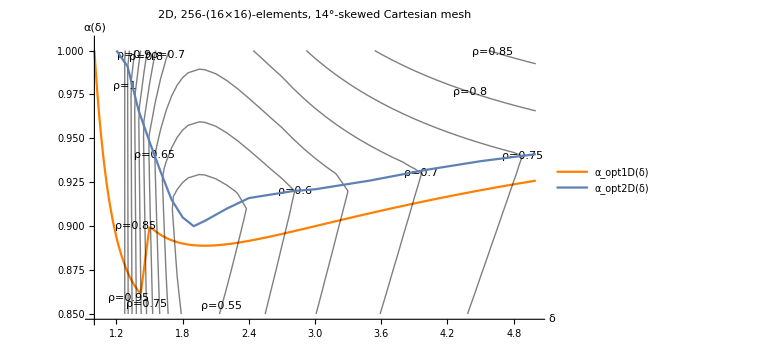

```mathematica
Show[
Plot[α[δ],{δ,1,5},PlotRange->{0.847,1.005},ImageSize->Large,AxesLabel->{"δ","α(δ)"},PlotStyle->Orange,PlotLegends->{"α_opt1D(δ)"},PlotLabel->"2D, 256-(16×16)-elements, 14°-skewed Cartesian mesh"],
ListContourPlot[
{
{1,0.85,2.42056},{1,0.86,2.43727},{1,0.87,2.45399},{1,0.88,2.4707},{1,0.89,2.48741},{1,0.9,2.50412},{1,0.91,2.52083},{1,0.92,2.53754},{1,0.93,2.55425},{1,0.94,2.57097},{1,0.95,2.58768},{1,0.96,2.60439},{1,0.97,2.6211},{1,0.98,2.63781},{1,0.99,2.65452},{1,1,2.67124},{1.05,0.85,1.5736},{1.05,0.86,1.58036},{1.05,0.87,1.58711},{1.05,0.88,1.59383},{1.05,0.89,1.60056},{1.05,0.9,1.60735},{1.05,0.91,1.61409},{1.05,0.92,1.62082},{1.05,0.93,1.62758},{1.05,0.94,1.63435},{1.05,0.95,1.6411},{1.05,0.96,1.64782},{1.05,0.97,1.65456},{1.05,0.98,1.66134},{1.05,0.99,1.66807},{1.05,1,1.67484},{1.1,0.85,1.39703},{1.1,0.86,1.4017},{1.1,0.87,1.40637},{1.1,0.88,1.41104},{1.1,0.89,1.41571},{1.1,0.9,1.42038},{1.1,0.91,1.42506},{1.1,0.92,1.42973},{1.1,0.93,1.4344},{1.1,0.94,1.43907},{1.1,0.95,1.44374},{1.1,0.96,1.44841},{1.1,0.97,1.45308},{1.1,0.98,1.45775},{1.1,0.99,1.46242},{1.1,1,1.4671},{1.15,0.85,1.25518},{1.15,0.86,1.25818},{1.15,0.87,1.26119},{1.15,0.88,1.26419},{1.15,0.89,1.26719},{1.15,0.9,1.27019},{1.15,0.91,1.2732},{1.15,0.92,1.2762},{1.15,0.93,1.2792},{1.15,0.94,1.2822},{1.15,0.95,1.28521},{1.15,0.96,1.28819},{1.15,0.97,1.29119},{1.15,0.98,1.29419},{1.15,0.99,1.2972},{1.15,1,1.3002},{1.2,0.85,1.13862},{1.2,0.86,1.14025},{1.2,0.87,1.14188},{1.2,0.88,1.14351},{1.2,0.89,1.14513},{1.2,0.9,1.14677},{1.2,0.91,1.1484},{1.2,0.92,1.15004},{1.2,0.93,1.15165},{1.2,0.94,1.15328},{1.2,0.95,1.15491},{1.2,0.96,1.15654},{1.2,0.97,1.15817},{1.2,0.98,1.1598},{1.2,0.99,1.16143},{1.2,1,1.16307},{1.25,0.85,1.04112},{1.25,0.86,1.0416},{1.25,0.87,1.04208},{1.25,0.88,1.04257},{1.25,0.89,1.04306},{1.25,0.9,1.04354},{1.25,0.91,1.04401},{1.25,0.92,1.04449},{1.25,0.93,1.04498},{1.25,0.94,1.04546},{1.25,0.95,1.04594},{1.25,0.96,1.04643},{1.25,0.97,1.04691},{1.25,0.98,1.04739},{1.25,0.99,1.04788},{1.25,1,1.04837},{1.3,0.85,0.958377},{1.3,0.86,0.957881},{1.3,0.87,0.9574},{1.3,0.88,0.956901},{1.3,0.89,0.956412},{1.3,0.9,0.955919},{1.3,0.91,0.95543},{1.3,0.92,0.954936},{1.3,0.93,0.954447},{1.3,0.94,0.953958},{1.3,0.95,0.953465},{1.3,0.96,0.952976},{1.3,0.97,0.952487},{1.3,0.98,0.951998},{1.3,0.99,0.951509},{1.3,1,0.969069},{1.35,0.85,0.887289},{1.35,0.86,0.885963},{1.35,0.87,0.884636},{1.35,0.88,0.883308},{1.35,0.89,0.881987},{1.35,0.9,0.880655},{1.35,0.91,0.879326},{1.35,0.92,0.878},{1.35,0.93,0.876671},{1.35,0.94,0.875345},{1.35,0.95,0.874019},{1.35,0.96,0.872689},{1.35,0.97,0.871363},{1.35,0.98,0.8774},{1.35,0.99,0.896557},{1.35,1,0.915715},{1.4,0.85,0.825579},{1.4,0.86,0.823528},{1.4,0.87,0.82148},{1.4,0.88,0.819427},{1.4,0.89,0.817374},{1.4,0.9,0.815321},{1.4,0.91,0.813264},{1.4,0.92,0.81121},{1.4,0.93,0.809158},{1.4,0.94,0.807103},{1.4,0.95,0.80505},{1.4,0.96,0.802994},{1.4,0.97,0.810645},{1.4,0.98,0.829312},{1.4,0.99,0.847978},{1.4,1,0.866645},{1.45,0.85,0.771534},{1.45,0.86,0.768845},{1.45,0.87,0.766159},{1.45,0.88,0.763469},{1.45,0.89,0.760781},{1.45,0.9,0.758092},{1.45,0.91,0.755404},{1.45,0.92,0.752718},{1.45,0.93,0.750028},{1.45,0.94,0.747337},{1.45,0.95,0.744647},{1.45,0.96,0.749131},{1.45,0.97,0.767347},{1.45,0.98,0.785568},{1.45,0.99,0.803788},{1.45,1,0.822009},{1.5,0.85,0.723842},{1.5,0.86,0.720592},{1.5,0.87,0.717344},{1.5,0.88,0.714096},{1.5,0.89,0.710847},{1.5,0.9,0.707598},{1.5,0.91,0.704348},{1.5,0.92,0.701099},{1.5,0.93,0.697849},{1.5,0.94,0.694598},{1.5,0.95,0.694255},{1.5,0.96,0.712087},{1.5,0.97,0.72992},{1.5,0.98,0.747751},{1.5,0.99,0.765587},{1.5,1,0.783439},{1.55,0.85,0.681497},{1.55,0.86,0.677749},{1.55,0.87,0.674},{1.55,0.88,0.670255},{1.55,0.89,0.666508},{1.55,0.9,0.662762},{1.55,0.91,0.659015},{1.55,0.92,0.655268},{1.55,0.93,0.65152},{1.55,0.94,0.647773},{1.55,0.95,0.664705},{1.55,0.96,0.682226},{1.55,0.97,0.699751},{1.55,0.98,0.717272},{1.55,0.99,0.734796},{1.55,1,0.752328},{1.6,0.85,0.643748},{1.6,0.86,0.639557},{1.6,0.87,0.635364},{1.6,0.88,0.631175},{1.6,0.89,0.626984},{1.6,0.9,0.622793},{1.6,0.91,0.618601},{1.6,0.92,0.61441},{1.6,0.93,0.61022},{1.6,0.94,0.623914},{1.6,0.95,0.64119},{1.6,0.96,0.658466},{1.6,0.97,0.675742},{1.6,0.98,0.693018},{1.6,0.99,0.710294},{1.6,1,0.727574},{1.65,0.85,0.610215},{1.65,0.86,0.60563},{1.65,0.87,0.601042},{1.65,0.88,0.596452},{1.65,0.89,0.591867},{1.65,0.9,0.587282},{1.65,0.91,0.582697},{1.65,0.92,0.578112},{1.65,0.93,0.588723},{1.65,0.94,0.605806},{1.65,0.95,0.622888},{1.65,0.96,0.63997},{1.65,0.97,0.657055},{1.65,0.98,0.674138},{1.65,0.99,0.69122},{1.65,1,0.708309},{1.7,0.85,0.582148},{1.7,0.86,0.577234},{1.7,0.87,0.572329},{1.7,0.88,0.567414},{1.7,0.89,0.562497},{1.7,0.9,0.557581},{1.7,0.91,0.552628},{1.7,0.92,0.558256},{1.7,0.93,0.575193},{1.7,0.94,0.592129},{1.7,0.95,0.609064},{1.7,0.96,0.626004},{1.7,0.97,0.642943},{1.7,0.98,0.659887},{1.7,0.99,0.676826},{1.7,1,0.693764},{1.75,0.85,0.56102},{1.75,0.86,0.555858},{1.75,0.87,0.5507},{1.75,0.88,0.545536},{1.75,0.89,0.540372},{1.75,0.9,0.535207},{1.75,0.91,0.531687},{1.75,0.92,0.548518},{1.75,0.93,0.565349},{1.75,0.94,0.582179},{1.75,0.95,0.599019},{1.75,0.96,0.615853},{1.75,0.97,0.632683},{1.75,0.98,0.649514},{1.75,0.99,0.666347},{1.75,1,0.683176},{1.8,0.85,0.54614},{1.8,0.86,0.540802},{1.8,0.87,0.535445},{1.8,0.88,0.530105},{1.8,0.89,0.524766},{1.8,0.9,0.519427},{1.8,0.91,0.525004},{1.8,0.92,0.541761},{1.8,0.93,0.558527},{1.8,0.94,0.57529},{1.8,0.95,0.592049},{1.8,0.96,0.608806},{1.8,0.97,0.625564},{1.8,0.98,0.642323},{1.8,0.99,0.659078},{1.8,1,0.675839},{1.85,0.85,0.536545},{1.85,0.86,0.5311},{1.85,0.87,0.525639},{1.85,0.88,0.520187},{1.85,0.89,0.514738},{1.85,0.9,0.504029},{1.85,0.91,0.520735},{1.85,0.92,0.537456},{1.85,0.93,0.554166},{1.85,0.94,0.57088},{1.85,0.95,0.587591},{1.85,0.96,0.604303},{1.85,0.97,0.621011},{1.85,0.98,0.637724},{1.85,0.99,0.654437},{1.85,1,0.671149},{1.95,0.85,0.53083},{1.95,0.86,0.525322},{1.95,0.87,0.51979},{1.95,0.88,0.514198},{1.95,0.89,0.508692},{1.95,0.9,0.503181},{1.95,0.91,0.517618},{1.95,0.92,0.534299},{1.95,0.93,0.550976},{1.95,0.94,0.567651},{1.95,0.95,0.584331},{1.95,0.96,0.601008},{1.95,0.97,0.617685},{1.95,0.98,0.634361},{1.95,0.99,0.651039},{1.95,1,0.667717},{2,0.85,0.535152},{2,0.86,0.529674},{2,0.87,0.5242},{2,0.88,0.518735},{2,0.89,0.513251},{2,0.9,0.507784},{2,0.91,0.518049},{2,0.92,0.534732},{2,0.93,0.551418},{2,0.94,0.568099},{2,0.95,0.58478},{2,0.96,0.601461},{2,0.97,0.618145},{2,0.98,0.634825},{2,0.99,0.65151},{2,1,0.668192},{2,1,0.668192},{2.1,0.85,0.546034},{2.1,0.86,0.540687},{2.1,0.87,0.535347},{2.1,0.88,0.530007},{2.1,0.89,0.524667},{2.1,0.9,0.519317},{2.1,0.91,0.521606},{2.1,0.92,0.53833},{2.1,0.93,0.555047},{2.1,0.94,0.571772},{2.1,0.95,0.588491},{2.1,0.96,0.605216},{2.1,0.97,0.621933},{2.1,0.98,0.638656},{2.1,0.99,0.655379},{2.1,1,0.6721},{2.2,0.85,0.557924},{2.2,0.86,0.552721},{2.2,0.87,0.547518},{2.2,0.88,0.542317},{2.2,0.89,0.537117},{2.2,0.9,0.531919},{2.2,0.91,0.526714},{2.2,0.92,0.544381},{2.2,0.93,0.561166},{2.2,0.94,0.577949},{2.2,0.95,0.594738},{2.2,0.96,0.611512},{2.2,0.97,0.628316},{2.2,0.98,0.645093},{2.2,0.99,0.661882},{2.2,1,0.678678},{2.3,0.85,0.570153},{2.3,0.86,0.565096},{2.3,0.87,0.560035},{2.3,0.88,0.554979},{2.3,0.89,0.549925},{2.3,0.9,0.544869},{2.3,0.91,0.539809},{2.3,0.92,0.551941},{2.3,0.93,0.568808},{2.3,0.94,0.585678},{2.3,0.95,0.602543},{2.3,0.96,0.619406},{2.3,0.97,0.636287},{2.3,0.98,0.653157},{2.3,0.99,0.67003},{2.3,1,0.686903},{2.4,0.85,0.582388},{2.4,0.86,0.577471},{2.4,0.87,0.572559},{2.4,0.88,0.567648},{2.4,0.89,0.562738},{2.4,0.9,0.557825},{2.4,0.91,0.552911},{2.4,0.92,0.560389},{2.4,0.93,0.577358},{2.4,0.94,0.594336},{2.4,0.95,0.611307},{2.4,0.96,0.628267},{2.4,0.97,0.645252},{2.4,0.98,0.662178},{2.4,0.99,0.67915},{2.4,1,0.696139},{2.5,0.85,0.594441},{2.5,0.86,0.589668},{2.5,0.87,0.584899},{2.5,0.88,0.580127},{2.5,0.89,0.575359},{2.5,0.9,0.570588},{2.5,0.91,0.56581},{2.5,0.92,0.569431},{2.5,0.93,0.58649},{2.5,0.94,0.603521},{2.5,0.95,0.620575},{2.5,0.96,0.637625},{2.5,0.97,0.654686},{2.5,0.98,0.671787},{2.5,0.99,0.688851},{2.5,1,0.705891},{2.6,0.85,0.606188},{2.6,0.86,0.601562},{2.6,0.87,0.59693},{2.6,0.88,0.5923},{2.6,0.89,0.587668},{2.6,0.9,0.583028},{2.6,0.91,0.578393},{2.6,0.92,0.578695},{2.6,0.93,0.595825},{2.6,0.94,0.61295},{2.6,0.95,0.63011},{2.6,0.96,0.647267},{2.6,0.97,0.664411},{2.6,0.98,0.681613},{2.6,0.99,0.698787},{2.6,1,0.715929},{2.7,0.85,0.617573},{2.7,0.86,0.613082},{2.7,0.87,0.60858},{2.7,0.88,0.604088},{2.7,0.89,0.59959},{2.7,0.9,0.595081},{2.7,0.91,0.590585},{2.7,0.92,0.58771},{2.7,0.93,0.604962},{2.7,0.94,0.622218},{2.7,0.95,0.639472},{2.7,0.96,0.656807},{2.7,0.97,0.674045},{2.7,0.98,0.691282},{2.7,0.99,0.708607},{2.7,1,0.72589},{2.8,0.85,0.628555},{2.8,0.86,0.624181},{2.8,0.87,0.619812},{2.8,0.88,0.615445},{2.8,0.89,0.611078},{2.8,0.9,0.606697},{2.8,0.91,0.602325},{2.8,0.92,0.598299},{2.8,0.93,0.615673},{2.8,0.94,0.633039},{2.8,0.95,0.650409},{2.8,0.96,0.667818},{2.8,0.97,0.685182},{2.8,0.98,0.702534},{2.8,0.99,0.719931},{2.8,1,0.737324},{2.9,0.85,0.639087},{2.9,0.86,0.634835},{2.9,0.87,0.630594},{2.9,0.88,0.626345},{2.9,0.89,0.622107},{2.9,0.9,0.61785},{2.9,0.91,0.613601},{2.9,0.92,0.60936},{2.9,0.93,0.625592},{2.9,0.94,0.643071},{2.9,0.95,0.660548},{2.9,0.96,0.678053},{2.9,0.97,0.695516},{2.9,0.98,0.713023},{2.9,0.99,0.730492},{2.9,1,0.747981},{3,0.85,0.649167},{3,0.86,0.645033},{3,0.87,0.640917},{3,0.88,0.636783},{3,0.89,0.632668},{3,0.9,0.628529},{3,0.91,0.624399},{3,0.92,0.620277},{3,0.93,0.634758},{3,0.94,0.652335},{3,0.95,0.66991},{3,0.96,0.687505},{3,0.97,0.70507},{3,0.98,0.722679},{3,0.99,0.740247},{3,1,0.757799},{3.1,0.85,0.658813},{3.1,0.86,0.654797},{3.1,0.87,0.650782},{3.1,0.88,0.646768},{3.1,0.89,0.642757},{3.1,0.9,0.638736},{3.1,0.91,0.63472},{3.1,0.92,0.630711},{3.1,0.93,0.64324},{3.1,0.94,0.660908},{3.1,0.95,0.678568},{3.1,0.96,0.696255},{3.1,0.97,0.713914},{3.1,0.98,0.731617},{3.1,0.99,0.749271},{3.1,1,0.766912},{3.2,0.85,0.668013},{3.2,0.86,0.664097},{3.2,0.87,0.660201},{3.2,0.88,0.656298},{3.2,0.89,0.652395},{3.2,0.9,0.648496},{3.2,0.91,0.644575},{3.2,0.92,0.640665},{3.2,0.93,0.651108},{3.2,0.94,0.668855},{3.2,0.95,0.686605},{3.2,0.96,0.704402},{3.2,0.97,0.722126},{3.2,0.98,0.739865},{3.2,0.99,0.757645},{3.2,1,0.775364},{3.3,0.85,0.676788},{3.3,0.86,0.672996},{3.3,0.87,0.669187},{3.3,0.88,0.665394},{3.3,0.89,0.661589},{3.3,0.9,0.657797},{3.3,0.91,0.653978},{3.3,0.92,0.650172},{3.3,0.93,0.658426},{3.3,0.94,0.676251},{3.3,0.95,0.69408},{3.3,0.96,0.711908},{3.3,0.97,0.729782},{3.3,0.98,0.747582},{3.3,0.99,0.765436},{3.3,1,0.783221},{3.4,0.85,0.685177},{3.4,0.86,0.681467},{3.4,0.87,0.677758},{3.4,0.88,0.674068},{3.4,0.89,0.670361},{3.4,0.9,0.666672},{3.4,0.91,0.66295},{3.4,0.92,0.659242},{3.4,0.93,0.665248},{3.4,0.94,0.683147},{3.4,0.95,0.701043},{3.4,0.96,0.718946},{3.4,0.97,0.736893},{3.4,0.98,0.754771},{3.4,0.99,0.772697},{3.4,1,0.790562},{3.5,0.85,0.693166},{3.5,0.86,0.689566},{3.5,0.87,0.685953},{3.5,0.88,0.682349},{3.5,0.89,0.678737},{3.5,0.9,0.675134},{3.5,0.91,0.67151},{3.5,0.92,0.667896},{3.5,0.93,0.671618},{3.5,0.94,0.68959},{3.5,0.95,0.707556},{3.5,0.96,0.725527},{3.5,0.97,0.743499},{3.5,0.98,0.761514},{3.5,0.99,0.779482},{3.5,1,0.797421},{3.6,0.85,0.700806},{3.6,0.86,0.697282},{3.6,0.87,0.693758},{3.6,0.88,0.690246},{3.6,0.89,0.686728},{3.6,0.9,0.683216},{3.6,0.91,0.67968},{3.6,0.92,0.676167},{3.6,0.93,0.677589},{3.6,0.94,0.69562},{3.6,0.95,0.713655},{3.6,0.96,0.731686},{3.6,0.97,0.749722},{3.6,0.98,0.767804},{3.6,0.99,0.785836},{3.6,1,0.803822},{3.7,0.85,0.708087},{3.7,0.86,0.704664},{3.7,0.87,0.701226},{3.7,0.88,0.697787},{3.7,0.89,0.694358},{3.7,0.9,0.690929},{3.7,0.91,0.687481},{3.7,0.92,0.684054},{3.7,0.93,0.683191},{3.7,0.94,0.701284},{3.7,0.95,0.71938},{3.7,0.96,0.737471},{3.7,0.97,0.755567},{3.7,0.98,0.773707},{3.7,0.99,0.791768},{3.7,1,0.809846},{3.8,0.85,0.715058},{3.8,0.86,0.711703},{3.8,0.87,0.708348},{3.8,0.88,0.704999},{3.8,0.89,0.701653},{3.8,0.9,0.698298},{3.8,0.91,0.694933},{3.8,0.92,0.691589},{3.8,0.93,0.68846},{3.8,0.94,0.706609},{3.8,0.95,0.724757},{3.8,0.96,0.74291},{3.8,0.97,0.761058},{3.8,0.98,0.779257},{3.8,0.99,0.797403},{3.8,1,0.81551},{3.9,0.85,0.721709},{3.9,0.86,0.718431},{3.9,0.87,0.715154},{3.9,0.88,0.711894},{3.9,0.89,0.708622},{3.9,0.9,0.705343},{3.9,0.91,0.702056},{3.9,0.92,0.698792},{3.9,0.93,0.695513},{3.9,0.94,0.711625},{3.9,0.95,0.729827},{3.9,0.96,0.748029},{3.9,0.97,0.766236},{3.9,0.98,0.784484},{3.9,0.99,0.80268},{3.9,1,0.820843},{4,0.85,0.728084},{4,0.86,0.724884},{4,0.87,0.721683},{4,0.88,0.718483},{4,0.89,0.715288},{4,0.9,0.712086},{4,0.91,0.708904},{4,0.92,0.705681},{4,0.93,0.702477},{4,0.94,0.716359},{4,0.95,0.734612},{4,0.96,0.752864},{4,0.97,0.771116},{4,0.98,0.789417},{4,0.99,0.807664},{4,1,0.825897},{4.1,0.85,0.734175},{4.1,0.86,0.731046},{4.1,0.87,0.727917},{4.1,0.88,0.724796},{4.1,0.89,0.721669},{4.1,0.9,0.718545},{4.1,0.91,0.715427},{4.1,0.92,0.712276},{4.1,0.93,0.709144},{4.1,0.94,0.720828},{4.1,0.95,0.739133},{4.1,0.96,0.757434},{4.1,0.97,0.775734},{4.1,0.98,0.794078},{4.1,0.99,0.812372},{4.1,1,0.830652},{4.2,0.85,0.740008},{4.2,0.86,0.736947},{4.2,0.87,0.733887},{4.2,0.88,0.730838},{4.2,0.89,0.72778},{4.2,0.9,0.724728},{4.2,0.91,0.721675},{4.2,0.92,0.718593},{4.2,0.93,0.715543},{4.2,0.94,0.725062},{4.2,0.95,0.743409},{4.2,0.96,0.761754},{4.2,0.97,0.780105},{4.2,0.98,0.79849},{4.2,0.99,0.81683},{4.2,1,0.835153},{4.3,0.85,0.745615},{4.3,0.86,0.742622},{4.3,0.87,0.739627},{4.3,0.88,0.73663},{4.3,0.89,0.733645},{4.3,0.9,0.730654},{4.3,0.91,0.727661},{4.3,0.92,0.724647},{4.3,0.93,0.721664},{4.3,0.94,0.729076},{4.3,0.95,0.747466},{4.3,0.96,0.765855},{4.3,0.97,0.784243},{4.3,0.98,0.802673},{4.3,0.99,0.821057},{4.3,1,0.839419},{4.4,0.85,0.75098},{4.4,0.86,0.74805},{4.4,0.87,0.745118},{4.4,0.88,0.742193},{4.4,0.89,0.739265},{4.4,0.9,0.736339},{4.4,0.91,0.73341},{4.4,0.92,0.730454},{4.4,0.93,0.727536},{4.4,0.94,0.732887},{4.4,0.95,0.751317},{4.4,0.96,0.769747},{4.4,0.97,0.788176},{4.4,0.98,0.806626},{4.4,0.99,0.825069},{4.4,1,0.843468},{4.5,0.85,0.756129},{4.5,0.86,0.75326},{4.5,0.87,0.750386},{4.5,0.88,0.747526},{4.5,0.89,0.744659},{4.5,0.9,0.741795},{4.5,0.91,0.738922},{4.5,0.92,0.736044},{4.5,0.93,0.733171},{4.5,0.94,0.736508},{4.5,0.95,0.754977},{4.5,0.96,0.773446},{4.5,0.97,0.791914},{4.5,0.98,0.810418},{4.5,0.99,0.828883},{4.5,1,0.847317},{4.6,0.85,0.761075},{4.6,0.86,0.758263},{4.6,0.87,0.755465},{4.6,0.88,0.752649},{4.6,0.89,0.74984},{4.6,0.9,0.747036},{4.6,0.91,0.744222},{4.6,0.92,0.741399},{4.6,0.93,0.738585},{4.6,0.94,0.739955},{4.6,0.95,0.758461},{4.6,0.96,0.776966},{4.6,0.97,0.795471},{4.6,0.98,0.813993},{4.6,0.99,0.832507},{4.6,1,0.85098},{4.7,0.85,0.765846},{4.7,0.86,0.763092},{4.7,0.87,0.760331},{4.7,0.88,0.757573},{4.7,0.89,0.75482},{4.7,0.9,0.752073},{4.7,0.91,0.749317},{4.7,0.92,0.746579},{4.7,0.93,0.743787},{4.7,0.94,0.743238},{4.7,0.95,0.76178},{4.7,0.96,0.780321},{4.7,0.97,0.798861},{4.7,0.98,0.817417},{4.7,0.99,0.835971},{4.7,1,0.854471},{4.8,0.85,0.77042},{4.8,0.86,0.767721},{4.8,0.87,0.765009},{4.8,0.88,0.762318},{4.8,0.89,0.75961},{4.8,0.9,0.756918},{4.8,0.91,0.754205},{4.8,0.92,0.751535},{4.8,0.93,0.748791},{4.8,0.94,0.74637},{4.8,0.95,0.764946},{4.8,0.96,0.78352},{4.8,0.97,0.802094},{4.8,0.98,0.820702},{4.8,0.99,0.839269},{4.8,1,0.857823},{4.9,0.85,0.774823},{4.9,0.86,0.772175},{4.9,0.87,0.769531},{4.9,0.88,0.766876},{4.9,0.89,0.76422},{4.9,0.9,0.761581},{4.9,0.91,0.758921},{4.9,0.92,0.756298},{4.9,0.93,0.753606},{4.9,0.94,0.750972},{4.9,0.95,0.767969},{4.9,0.96,0.786575},{4.9,0.97,0.805181},{4.9,0.98,0.82382},{4.9,0.99,0.842418},{4.9,1,0.861004},{5,0.85,0.779064},{5,0.86,0.776466},{5,0.87,0.773869},{5,0.88,0.771266},{5,0.89,0.768673},{5,0.9,0.76607},{5,0.91,0.763461},{5,0.92,0.760887},{5,0.93,0.758244},{5,0.94,0.75566},{5,0.95,0.770858},{5,0.96,0.789496},{5,0.97,0.808132},{5,0.98,0.826801},{5,0.99,0.845425},{5,1,0.864046}
}
,Contours->{0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1},ContourShading->None,ContourLabels->(Text[StringJoin["ρ=",ToString[#3]],{#1,#2}]&)],
ListPlot[
{
{1.2,1},{1.3,0.991},{1.4,0.966},{1.5,0.948},{1.6,0.931},{1.7,0.915},{1.8,0.905},{1.9,0.900},{2,0.903},{2.2,0.91},{2.4,0.916},{2.6,0.918},{2.8,0.920},{3.0,0.921},{3.5,0.926},{4,0.932},{4.5,0.937},{5,0.941}
},
PlotStyle->PointSize[0.005],Joined->True,PlotLegends->{"α_opt2D(δ)"}
]
]
```

```mathematica
.b4
```

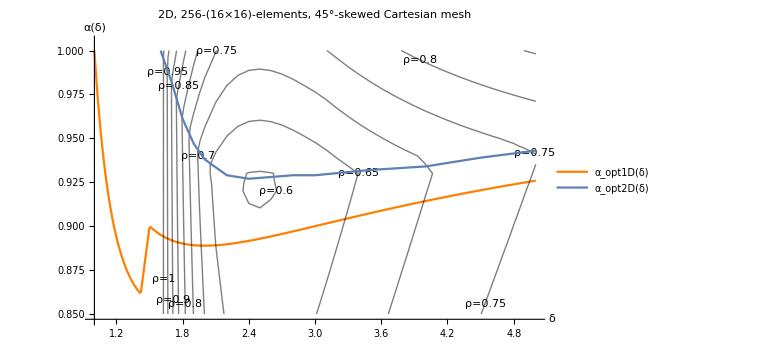

```mathematica
Show[
Plot[α[δ],{δ,1,5},PlotRange->{0.847,1.005},AxesLabel->{"δ","α(δ)"},PlotStyle->Orange,ImageSize->Large,PlotLegends->{"α_opt1D(δ)"},PlotLabel->"2D, 256-(16×16)-elements, 45°-skewed Cartesian mesh"],
ListContourPlot[
{
{1.5,0.85,1.19858},{1.5,0.86,1.2009},{1.5,0.87,1.20321},{1.5,0.88,1.20551},{1.5,0.89,1.2078},{1.5,0.9,1.21009},{1.5,0.91,1.21238},{1.5,0.92,1.21467},{1.5,0.93,1.21698},{1.5,0.94,1.21928},{1.5,0.95,1.22159},{1.5,0.96,1.2239},{1.5,0.97,1.22623},{1.5,0.98,1.22856},{1.5,0.99,1.23089},{1.5,1,1.23318},{1.55,0.85,1.10924},{1.55,0.86,1.11053},{1.55,0.87,1.11182},{1.55,0.88,1.1131},{1.55,0.89,1.11439},{1.55,0.9,1.11567},{1.55,0.91,1.11696},{1.55,0.92,1.11824},{1.55,0.93,1.11952},{1.55,0.94,1.1208},{1.55,0.95,1.12208},{1.55,0.96,1.12337},{1.55,0.97,1.12464},{1.55,0.98,1.12593},{1.55,0.99,1.1272},{1.55,1,1.1285},{1.6,0.85,1.03337},{1.6,0.86,1.03376},{1.6,0.87,1.03415},{1.6,0.88,1.03454},{1.6,0.89,1.03493},{1.6,0.9,1.03533},{1.6,0.91,1.03572},{1.6,0.92,1.03611},{1.6,0.93,1.03651},{1.6,0.94,1.03689},{1.6,0.95,1.03728},{1.6,0.96,1.03767},{1.6,0.97,1.03806},{1.6,0.98,1.03846},{1.6,0.99,1.03884},{1.6,1,1.03925},{1.65,0.85,0.967939},{1.65,0.86,0.967561},{1.65,0.87,0.967182},{1.65,0.88,0.966803},{1.65,0.89,0.966426},{1.65,0.9,0.966049},{1.65,0.91,0.965673},{1.65,0.92,0.965301},{1.65,0.93,0.964913},{1.65,0.94,0.964533},{1.65,0.95,0.964149},{1.65,0.96,0.963769},{1.65,0.97,0.963407},{1.65,0.98,0.963031},{1.65,0.99,0.96266},{1.65,1,0.970599},{1.7,0.85,0.911064},{1.7,0.86,0.91002},{1.7,0.87,0.908971},{1.7,0.88,0.907922},{1.7,0.89,0.906875},{1.7,0.9,0.905831},{1.7,0.91,0.904788},{1.7,0.92,0.903737},{1.7,0.93,0.902686},{1.7,0.94,0.901638},{1.7,0.95,0.900579},{1.7,0.96,0.899546},{1.7,0.97,0.898507},{1.7,0.98,0.89744},{1.7,0.99,0.912065},{1.7,1,0.931391},{1.75,0.85,0.861432},{1.75,0.86,0.859792},{1.75,0.87,0.85816},{1.75,0.88,0.856533},{1.75,0.89,0.854902},{1.75,0.9,0.853276},{1.75,0.91,0.851636},{1.75,0.92,0.85},{1.75,0.93,0.848361},{1.75,0.94,0.846743},{1.75,0.95,0.845108},{1.75,0.96,0.843481},{1.75,0.97,0.841837},{1.75,0.98,0.85846},{1.75,0.99,0.877421},{1.75,1,0.896387},{1.8,0.85,0.81812},{1.8,0.86,0.815978},{1.8,0.87,0.813832},{1.8,0.88,0.811704},{1.8,0.89,0.809565},{1.8,0.9,0.807433},{1.8,0.91,0.805272},{1.8,0.92,0.803119},{1.8,0.93,0.800983},{1.8,0.94,0.798807},{1.8,0.95,0.79668},{1.8,0.96,0.794534},{1.8,0.97,0.809428},{1.8,0.98,0.828085},{1.8,0.99,0.846739},{1.8,1,0.865393},{1.85,0.85,0.780552},{1.85,0.86,0.77797},{1.85,0.87,0.775387},{1.85,0.88,0.772812},{1.85,0.89,0.770236},{1.85,0.9,0.767644},{1.85,0.91,0.765041},{1.85,0.92,0.762466},{1.85,0.93,0.759873},{1.85,0.94,0.757285},{1.85,0.95,0.754711},{1.85,0.96,0.764684},{1.85,0.97,0.783068},{1.85,0.98,0.801451},{1.85,0.99,0.819832},{1.85,1,0.838215},{1.9,0.85,0.748328},{1.9,0.86,0.745364},{1.9,0.87,0.742406},{1.9,0.88,0.739443},{1.9,0.89,0.73648},{1.9,0.9,0.733517},{1.9,0.91,0.730544},{1.9,0.92,0.727588},{1.9,0.93,0.724635},{1.9,0.94,0.721671},{1.9,0.95,0.72393},{1.9,0.96,0.742078},{1.9,0.97,0.760224},{1.9,0.98,0.778372},{1.9,0.99,0.796518},{1.9,1,0.814665},{1.95,0.85,0.721115},{1.95,0.86,0.717835},{1.95,0.87,0.714551},{1.95,0.88,0.711271},{1.95,0.89,0.707988},{1.95,0.9,0.704705},{1.95,0.91,0.70141},{1.95,0.92,0.698128},{1.95,0.93,0.694852},{1.95,0.94,0.691569},{1.95,0.95,0.704771},{1.95,0.96,0.722716},{1.95,0.97,0.74066},{1.95,0.98,0.758605},{1.95,0.99,0.77655},{1.95,1,0.794497},{2,0.85,0.698521},{2,0.86,0.694973},{2,0.87,0.691426},{2,0.88,0.68788},{2,0.89,0.684319},{2,0.9,0.680773},{2,0.91,0.677227},{2,0.92,0.67368},{2,0.93,0.670133},{2,0.94,0.670798},{2,0.95,0.688572},{2,0.96,0.706347},{2,0.97,0.724121},{2,0.98,0.741892},{2,0.99,0.759666},{2,1,0.777441},{2.1,0.85,0.665346},{2.1,0.86,0.661409},{2.1,0.87,0.657473},{2.1,0.88,0.653535},{2.1,0.89,0.649577},{2.1,0.9,0.645641},{2.1,0.91,0.641705},{2.1,0.92,0.637767},{2.1,0.93,0.628919},{2.1,0.94,0.646435},{2.1,0.95,0.66395},{2.1,0.96,0.681465},{2.1,0.97,0.69898},{2.1,0.98,0.716503},{2.1,0.99,0.734019},{2.1,1,0.751534},{2.2,0.85,0.644677},{2.2,0.86,0.640497},{2.2,0.87,0.636316},{2.2,0.88,0.632136},{2.2,0.89,0.62794},{2.2,0.9,0.623764},{2.2,0.91,0.619583},{2.2,0.92,0.615405},{2.2,0.93,0.613139},{2.2,0.94,0.630484},{2.2,0.95,0.647829},{2.2,0.96,0.665182},{2.2,0.97,0.68253},{2.2,0.98,0.699876},{2.2,0.99,0.717219},{2.2,1,0.734563},{2.3,0.85,0.632976},{2.3,0.86,0.628658},{2.3,0.87,0.624342},{2.3,0.88,0.620021},{2.3,0.89,0.615702},{2.3,0.9,0.611377},{2.3,0.91,0.607061},{2.3,0.92,0.602724},{2.3,0.93,0.603722},{2.3,0.94,0.620964},{2.3,0.95,0.638216},{2.3,0.96,0.655463},{2.3,0.97,0.672709},{2.3,0.98,0.689952},{2.3,0.99,0.707197},{2.3,1,0.72444},{2.4,0.85,0.627557},{2.4,0.86,0.623175},{2.4,0.87,0.618795},{2.4,0.88,0.614414},{2.4,0.89,0.610027},{2.4,0.9,0.605638},{2.4,0.91,0.601259},{2.4,0.92,0.596864},{2.4,0.93,0.599051},{2.4,0.94,0.616245},{2.4,0.95,0.633441},{2.4,0.96,0.650641},{2.4,0.97,0.667835},{2.4,0.98,0.685029},{2.4,0.99,0.702222},{2.4,1,0.719419},{2.5,0.85,0.626558},{2.5,0.86,0.622163},{2.5,0.87,0.617766},{2.5,0.88,0.61336},{2.5,0.89,0.608979},{2.5,0.9,0.604584},{2.5,0.91,0.600189},{2.5,0.92,0.595794},{2.5,0.93,0.59787},{2.5,0.94,0.615055},{2.5,0.95,0.63224},{2.5,0.96,0.649425},{2.5,0.97,0.666604},{2.5,0.98,0.683784},{2.5,0.99,0.700965},{2.5,1,0.718141},{2.6,0.85,0.628549},{2.6,0.86,0.624168},{2.6,0.87,0.619812},{2.6,0.88,0.615421},{2.6,0.89,0.611047},{2.6,0.9,0.606695},{2.6,0.91,0.602321},{2.6,0.92,0.59796},{2.6,0.93,0.599249},{2.6,0.94,0.616462},{2.6,0.95,0.633656},{2.6,0.96,0.650851},{2.6,0.97,0.668044},{2.6,0.98,0.685238},{2.6,0.99,0.702438},{2.6,1,0.719604},{2.7,0.85,0.632327},{2.7,0.86,0.627998},{2.7,0.87,0.623668},{2.7,0.88,0.61933},{2.7,0.89,0.615016},{2.7,0.9,0.610699},{2.7,0.91,0.606359},{2.7,0.92,0.602037},{2.7,0.93,0.602478},{2.7,0.94,0.619763},{2.7,0.95,0.63699},{2.7,0.96,0.654224},{2.7,0.97,0.671455},{2.7,0.98,0.688697},{2.7,0.99,0.705928},{2.7,1,0.723116},{2.8,0.85,0.637308},{2.8,0.86,0.633041},{2.8,0.87,0.6288},{2.8,0.88,0.624546},{2.8,0.89,0.620238},{2.8,0.9,0.615969},{2.8,0.91,0.611714},{2.8,0.92,0.607445},{2.8,0.93,0.607138},{2.8,0.94,0.624504},{2.8,0.95,0.641796},{2.8,0.96,0.659088},{2.8,0.97,0.676386},{2.8,0.98,0.693684},{2.8,0.99,0.710968},{2.8,1,0.728134},{2.9,0.85,0.6432},{2.9,0.86,0.638985},{2.9,0.87,0.63475},{2.9,0.88,0.630551},{2.9,0.89,0.62635},{2.9,0.9,0.622179},{2.9,0.91,0.617992},{2.9,0.92,0.613771},{2.9,0.93,0.612979},{2.9,0.94,0.630344},{2.9,0.95,0.647693},{2.9,0.96,0.665037},{2.9,0.97,0.68239},{2.9,0.98,0.699739},{2.9,0.99,0.717095},{2.9,1,0.734368},{3,0.85,0.648972},{3,0.86,0.644833},{3,0.87,0.640692},{3,0.88,0.636553},{3,0.89,0.632433},{3,0.9,0.628307},{3,0.91,0.624181},{3,0.92,0.620062},{3,0.93,0.61929},{3,0.94,0.636588},{3,0.95,0.654005},{3,0.96,0.671409},{3,0.97,0.688826},{3,0.98,0.706241},{3,0.99,0.723658},{3,1,0.741029},{3.1,0.85,0.657081},{3.1,0.86,0.653056},{3.1,0.87,0.64902},{3.1,0.88,0.644975},{3.1,0.89,0.640938},{3.1,0.9,0.636898},{3.1,0.91,0.632875},{3.1,0.92,0.628864},{3.1,0.93,0.62643},{3.1,0.94,0.643916},{3.1,0.95,0.661401},{3.1,0.96,0.678932},{3.1,0.97,0.696411},{3.1,0.98,0.713894},{3.1,0.99,0.731395},{3.1,1,0.749386},{3.2,0.85,0.665186},{3.2,0.86,0.661221},{3.2,0.87,0.657312},{3.2,0.88,0.653374},{3.2,0.89,0.649417},{3.2,0.9,0.645489},{3.2,0.91,0.641541},{3.2,0.92,0.637651},{3.2,0.93,0.634819},{3.2,0.94,0.652397},{3.2,0.95,0.669974},{3.2,0.96,0.687597},{3.2,0.97,0.705149},{3.2,0.98,0.722721},{3.2,0.99,0.740294},{3.2,1,0.75789},{3.3,0.85,0.673109},{3.3,0.86,0.669243},{3.3,0.87,0.665421},{3.3,0.88,0.661575},{3.3,0.89,0.657726},{3.3,0.9,0.65388},{3.3,0.91,0.650022},{3.3,0.92,0.646233},{3.3,0.93,0.642681},{3.3,0.94,0.660346},{3.3,0.95,0.678009},{3.3,0.96,0.695725},{3.3,0.97,0.713358},{3.3,0.98,0.731012},{3.3,0.99,0.748692},{3.3,1,0.766353},{3.4,0.85,0.680818},{3.4,0.86,0.677047},{3.4,0.87,0.673313},{3.4,0.88,0.669554},{3.4,0.89,0.665805},{3.4,0.9,0.662045},{3.4,0.91,0.658292},{3.4,0.92,0.654539},{3.4,0.93,0.650784},{3.4,0.94,0.667784},{3.4,0.95,0.685527},{3.4,0.96,0.703324},{3.4,0.97,0.72104},{3.4,0.98,0.738771},{3.4,0.99,0.756529},{3.4,1,0.774231},{3.5,0.85,0.688291},{3.5,0.86,0.684645},{3.5,0.87,0.680974},{3.5,0.88,0.677307},{3.5,0.89,0.673636},{3.5,0.9,0.669976},{3.5,0.91,0.666305},{3.5,0.92,0.662669},{3.5,0.93,0.65898},{3.5,0.94,0.674741},{3.5,0.95,0.692558},{3.5,0.96,0.71043},{3.5,0.97,0.728222},{3.5,0.98,0.746045},{3.5,0.99,0.763856},{3.5,1,0.781632},{3.6,0.85,0.695539},{3.6,0.86,0.691955},{3.6,0.87,0.688388},{3.6,0.88,0.68479},{3.6,0.89,0.681216},{3.6,0.9,0.677628},{3.6,0.91,0.674048},{3.6,0.92,0.670494},{3.6,0.93,0.666878},{3.6,0.94,0.681257},{3.6,0.95,0.699144},{3.6,0.96,0.717085},{3.6,0.97,0.734948},{3.6,0.98,0.752845},{3.6,0.99,0.77072},{3.6,1,0.788563},{3.7,0.85,0.70251},{3.7,0.86,0.699007},{3.7,0.87,0.695533},{3.7,0.88,0.69202},{3.7,0.89,0.688521},{3.7,0.9,0.685023},{3.7,0.91,0.681518},{3.7,0.92,0.678009},{3.7,0.93,0.674516},{3.7,0.94,0.687372},{3.7,0.95,0.705324},{3.7,0.96,0.72333},{3.7,0.97,0.741258},{3.7,0.98,0.75922},{3.7,0.99,0.777167},{3.7,1,0.795068},{3.8,0.85,0.709228},{3.8,0.86,0.705804},{3.8,0.87,0.702415},{3.8,0.88,0.69898},{3.8,0.89,0.695562},{3.8,0.9,0.69214},{3.8,0.91,0.688728},{3.8,0.92,0.685288},{3.8,0.93,0.681875},{3.8,0.94,0.693133},{3.8,0.95,0.711135},{3.8,0.96,0.729203},{3.8,0.97,0.747189},{3.8,0.98,0.765212},{3.8,0.99,0.78322},{3.8,1,0.801157},{3.9,0.85,0.715711},{3.9,0.86,0.712367},{3.9,0.87,0.709035},{3.9,0.88,0.705682},{3.9,0.89,0.702341},{3.9,0.9,0.699},{3.9,0.91,0.695657},{3.9,0.92,0.692326},{3.9,0.93,0.688958},{3.9,0.94,0.698546},{3.9,0.95,0.716606},{3.9,0.96,0.734733},{3.9,0.97,0.752781},{3.9,0.98,0.77084},{3.9,0.99,0.78892},{3.9,1,0.806921},{4,0.85,0.721938},{4,0.86,0.718666},{4,0.87,0.715412},{4,0.88,0.71213},{4,0.89,0.708863},{4,0.9,0.705593},{4,0.91,0.702325},{4,0.92,0.699069},{4,0.93,0.695774},{4,0.94,0.703654},{4,0.95,0.721769},{4,0.96,0.739949},{4,0.97,0.758052},{4,0.98,0.776166},{4,0.99,0.794304},{4,1,0.812363},{4.1,0.85,0.727929},{4.1,0.86,0.724727},{4.1,0.87,0.721548},{4.1,0.88,0.718336},{4.1,0.89,0.715141},{4.1,0.9,0.71194},{4.1,0.91,0.70874},{4.1,0.92,0.705556},{4.1,0.93,0.702331},{4.1,0.94,0.70848},{4.1,0.95,0.726647},{4.1,0.96,0.744824},{4.1,0.97,0.763033},{4.1,0.98,0.781213},{4.1,0.99,0.799386},{4.1,1,0.817509},{4.2,0.85,0.733705},{4.2,0.86,0.730572},{4.2,0.87,0.727451},{4.2,0.88,0.724308},{4.2,0.89,0.721181},{4.2,0.9,0.718046},{4.2,0.91,0.714913},{4.2,0.92,0.71178},{4.2,0.93,0.708654},{4.2,0.94,0.713048},{4.2,0.95,0.731264},{4.2,0.96,0.74949},{4.2,0.97,0.76777},{4.2,0.98,0.785967},{4.2,0.99,0.804195},{4.2,1,0.822368},{4.3,0.85,0.739252},{4.3,0.86,0.736187},{4.3,0.87,0.733127},{4.3,0.88,0.730053},{4.3,0.89,0.726991},{4.3,0.9,0.723923},{4.3,0.91,0.720862},{4.3,0.92,0.717783},{4.3,0.93,0.714725},{4.3,0.94,0.717377},{4.3,0.95,0.73564},{4.3,0.96,0.753912},{4.3,0.97,0.772238},{4.3,0.98,0.790481},{4.3,0.99,0.808755},{4.3,1,0.82697},{4.4,0.85,0.744592},{4.4,0.86,0.741592},{4.4,0.87,0.738593},{4.4,0.88,0.735583},{4.4,0.89,0.732577},{4.4,0.9,0.729573},{4.4,0.91,0.726579},{4.4,0.92,0.72356},{4.4,0.93,0.720566},{4.4,0.94,0.721486},{4.4,0.95,0.739794},{4.4,0.96,0.75811},{4.4,0.97,0.776479},{4.4,0.98,0.794766},{4.4,0.99,0.813082},{4.4,1,0.831335},{4.5,0.85,0.749733},{4.5,0.86,0.746795},{4.5,0.87,0.743856},{4.5,0.88,0.740908},{4.5,0.89,0.737961},{4.5,0.9,0.735017},{4.5,0.91,0.732082},{4.5,0.92,0.729152},{4.5,0.93,0.726189},{4.5,0.94,0.725391},{4.5,0.95,0.743741},{4.5,0.96,0.762099},{4.5,0.97,0.780487},{4.5,0.98,0.798841},{4.5,0.99,0.817195},{4.5,1,0.835507},{4.6,0.85,0.754692},{4.6,0.86,0.751806},{4.6,0.87,0.748925},{4.6,0.88,0.746035},{4.6,0.89,0.743147},{4.6,0.9,0.74026},{4.6,0.91,0.737383},{4.6,0.92,0.734511},{4.6,0.93,0.731603},{4.6,0.94,0.729106},{4.6,0.95,0.747506},{4.6,0.96,0.765895},{4.6,0.97,0.784321},{4.6,0.98,0.802714},{4.6,0.99,0.821108},{4.6,1,0.839455},{4.7,0.85,0.759462},{4.7,0.86,0.756642},{4.7,0.87,0.753808},{4.7,0.88,0.750973},{4.7,0.89,0.748142},{4.7,0.9,0.745312},{4.7,0.91,0.742497},{4.7,0.92,0.739674},{4.7,0.93,0.736834},{4.7,0.94,0.734},{4.7,0.95,0.751084},{4.7,0.96,0.769512},{4.7,0.97,0.787938},{4.7,0.98,0.806404},{4.7,0.99,0.824834},{4.7,1,0.843216},{4.8,0.85,0.764059},{4.8,0.86,0.761294},{4.8,0.87,0.758514},{4.8,0.88,0.755733},{4.8,0.89,0.752957},{4.8,0.9,0.75018},{4.8,0.91,0.747419},{4.8,0.92,0.744653},{4.8,0.93,0.741862},{4.8,0.94,0.739082},{4.8,0.95,0.754496},{4.8,0.96,0.77296},{4.8,0.97,0.791424},{4.8,0.98,0.809926},{4.8,0.99,0.828393},{4.8,1,0.846802},{4.9,0.85,0.768493},{4.9,0.86,0.76578},{4.9,0.87,0.763052},{4.9,0.88,0.760322},{4.9,0.89,0.757599},{4.9,0.9,0.754874},{4.9,0.91,0.752165},{4.9,0.92,0.749452},{4.9,0.93,0.746709},{4.9,0.94,0.743981},{4.9,0.95,0.757753},{4.9,0.96,0.776253},{4.9,0.97,0.794752},{4.9,0.98,0.813287},{4.9,0.99,0.831788},{4.9,1,0.850249},{5,0.85,0.77277},{5,0.86,0.770108},{5,0.87,0.76743},{5,0.88,0.764749},{5,0.89,0.762077},{5,0.9,0.7594},{5,0.91,0.756744},{5,0.92,0.754082},{5,0.93,0.751384},{5,0.94,0.748723},{5,0.95,0.760867},{5,0.96,0.7794},{5,0.97,0.79794},{5,0.98,0.8165},{5,0.99,0.835033},{5,1,0.853566}
}
,Contours->{0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1},ContourShading->None,ContourLabels->(Text[StringJoin["ρ=",ToString[#3]],{#1,#2}]&)],
ListPlot[
{
{1.6,1},{1.7,0.982},{1.8,0.961},{1.9,0.947},{2,0.938},{2.2,0.929},{2.4,0.927},{2.6,0.928},{2.8,0.929},{3,0.929},{3.5,0.932},{4,0.934},{4.5,0.939},{5,0.943}
},
PlotStyle->PointSize[0.005],Joined->True,PlotLegends->{"α_opt2D(δ)"}
]
]
```

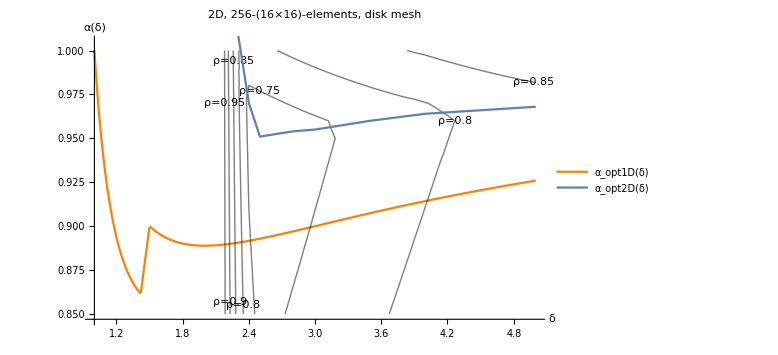

```mathematica
Show[
Plot[α[δ],{δ,1,5},PlotRange->{0.847,1.005},AxesLabel->{"δ","α(δ)"},PlotStyle->Orange,ImageSize->Large,PlotLegends->{"α_opt1D(δ)"},PlotLabel->"2D, 256-(16×16)-elements, disk mesh"],
ListContourPlot[
{
{2,0.85,1.28615},{2,0.86,1.28952},{2,0.87,1.29288},{2,0.88,1.29625},{2,0.89,1.29962},{2,0.9,1.30298},{2,0.91,1.30635},{2,0.92,1.30972},{2,0.93,1.31308},{2,0.94,1.31645},{2,0.95,1.31983},{2,0.96,1.3232},{2,0.97,1.32656},{2,0.98,1.32993},{2,0.99,1.3333},{2,1,1.33666},{2.1,0.85,1.07044},{2.1,0.86,1.07127},{2.1,0.87,1.0721},{2.1,0.88,1.07293},{2.1,0.89,1.07376},{2.1,0.9,1.07458},{2.1,0.91,1.07541},{2.1,0.92,1.07624},{2.1,0.93,1.07706},{2.1,0.94,1.07789},{2.1,0.95,1.07875},{2.1,0.96,1.07958},{2.1,0.97,1.08041},{2.1,0.98,1.08124},{2.1,0.99,1.08206},{2.1,1,1.08289},{2.2,0.85,0.928381},{2.2,0.86,0.927539},{2.2,0.87,0.926696},{2.2,0.88,0.925854},{2.2,0.89,0.925011},{2.2,0.9,0.924173},{2.2,0.91,0.923326},{2.2,0.92,0.922497},{2.2,0.93,0.921663},{2.2,0.94,0.920812},{2.2,0.95,0.919969},{2.2,0.96,0.919127},{2.2,0.97,0.918284},{2.2,0.98,0.917441},{2.2,0.99,0.916599},{2.2,1,0.915756},{2.3,0.85,0.832386},{2.3,0.86,0.830413},{2.3,0.87,0.828441},{2.3,0.88,0.826456},{2.3,0.89,0.824492},{2.3,0.9,0.82252},{2.3,0.91,0.820548},{2.3,0.92,0.818574},{2.3,0.93,0.816627},{2.3,0.94,0.814657},{2.3,0.95,0.812677},{2.3,0.96,0.810705},{2.3,0.97,0.808733},{2.3,0.98,0.806761},{2.3,0.99,0.804789},{2.3,1,0.802817},{2.4,0.85,0.766433},{2.4,0.86,0.763682},{2.4,0.87,0.760935},{2.4,0.88,0.758187},{2.4,0.89,0.755443},{2.4,0.9,0.752696},{2.4,0.91,0.749939},{2.4,0.92,0.747202},{2.4,0.93,0.744457},{2.4,0.94,0.741708},{2.4,0.95,0.738961},{2.4,0.96,0.736213},{2.4,0.97,0.733466},{2.4,0.98,0.74976},{2.4,0.99,0.767612},{2.4,1,0.785467},{2.5,0.85,0.735551},{2.5,0.86,0.732446},{2.5,0.87,0.729332},{2.5,0.88,0.726221},{2.5,0.89,0.723113},{2.5,0.9,0.72},{2.5,0.91,0.71689},{2.5,0.92,0.713768},{2.5,0.93,0.710661},{2.5,0.94,0.707553},{2.5,0.95,0.704443},{2.5,0.96,0.719602},{2.5,0.97,0.737515},{2.5,0.98,0.755425},{2.5,0.99,0.773337},{2.5,1,0.791254},{2.6,0.85,0.741957},{2.6,0.86,0.738919},{2.6,0.87,0.735885},{2.6,0.88,0.732844},{2.6,0.89,0.729813},{2.6,0.9,0.726773},{2.6,0.91,0.723743},{2.6,0.92,0.720703},{2.6,0.93,0.717669},{2.6,0.94,0.714634},{2.6,0.95,0.711592},{2.6,0.96,0.725024},{2.6,0.97,0.742994},{2.6,0.98,0.760978},{2.6,0.99,0.778944},{2.6,1,0.79691},{2.7,0.85,0.748285},{2.7,0.86,0.745329},{2.7,0.87,0.742366},{2.7,0.88,0.739408},{2.7,0.89,0.736445},{2.7,0.9,0.733486},{2.7,0.91,0.730526},{2.7,0.92,0.727569},{2.7,0.93,0.724592},{2.7,0.94,0.721633},{2.7,0.95,0.718674},{2.7,0.96,0.730274},{2.7,0.97,0.748299},{2.7,0.98,0.766338},{2.7,0.99,0.784361},{2.7,1,0.802385},{2.8,0.85,0.754482},{2.8,0.86,0.751596},{2.8,0.87,0.748706},{2.8,0.88,0.745814},{2.8,0.89,0.742925},{2.8,0.9,0.740042},{2.8,0.91,0.737154},{2.8,0.92,0.734273},{2.8,0.93,0.731368},{2.8,0.94,0.728482},{2.8,0.95,0.725595},{2.8,0.96,0.735308},{2.8,0.97,0.753388},{2.8,0.98,0.771476},{2.8,0.99,0.789549},{2.8,1,0.807631},{2.9,0.85,0.760495},{2.9,0.86,0.757677},{2.9,0.87,0.754857},{2.9,0.88,0.752042},{2.9,0.89,0.749225},{2.9,0.9,0.746402},{2.9,0.91,0.743584},{2.9,0.92,0.740777},{2.9,0.93,0.737942},{2.9,0.94,0.735128},{2.9,0.95,0.732312},{2.9,0.96,0.740142},{2.9,0.97,0.75825},{2.9,0.98,0.776397},{2.9,0.99,0.794519},{2.9,1,0.812649},{3,0.85,0.7663},{3,0.86,0.763554},{3,0.87,0.760804},{3,0.88,0.758048},{3,0.89,0.755301},{3,0.9,0.752559},{3,0.91,0.749807},{3,0.92,0.747062},{3,0.93,0.744294},{3,0.94,0.741549},{3,0.95,0.738802},{3,0.96,0.744736},{3,0.97,0.762914},{3,0.98,0.781096},{3,0.99,0.799264},{3,1,0.817445},{3.1,0.85,0.771902},{3.1,0.86,0.769218},{3.1,0.87,0.766535},{3.1,0.88,0.763848},{3.1,0.89,0.761167},{3.1,0.9,0.758483},{3.1,0.91,0.755796},{3.1,0.92,0.753122},{3.1,0.93,0.750443},{3.1,0.94,0.747735},{3.1,0.95,0.745055},{3.1,0.96,0.749112},{3.1,0.97,0.767339},{3.1,0.98,0.785581},{3.1,0.99,0.803804},{3.1,1,0.822021},{3.2,0.85,0.777289},{3.2,0.86,0.774668},{3.2,0.87,0.77204},{3.2,0.88,0.769426},{3.2,0.89,0.766799},{3.2,0.9,0.764179},{3.2,0.91,0.761569},{3.2,0.92,0.758949},{3.2,0.93,0.756337},{3.2,0.94,0.753686},{3.2,0.95,0.75107},{3.2,0.96,0.753309},{3.2,0.97,0.771581},{3.2,0.98,0.78986},{3.2,0.99,0.808128},{3.2,1,0.826384},{3.3,0.85,0.782468},{3.3,0.86,0.779907},{3.3,0.87,0.77734},{3.3,0.88,0.774787},{3.3,0.89,0.772226},{3.3,0.9,0.769666},{3.3,0.91,0.76711},{3.3,0.92,0.764555},{3.3,0.93,0.762003},{3.3,0.94,0.759419},{3.3,0.95,0.756849},{3.3,0.96,0.757309},{3.3,0.97,0.775594},{3.3,0.98,0.793945},{3.3,0.99,0.812258},{3.3,1,0.830552},{3.4,0.85,0.787442},{3.4,0.86,0.78494},{3.4,0.87,0.782432},{3.4,0.88,0.779938},{3.4,0.89,0.777438},{3.4,0.9,0.774941},{3.4,0.91,0.772431},{3.4,0.92,0.769935},{3.4,0.93,0.767448},{3.4,0.94,0.76491},{3.4,0.95,0.762415},{3.4,0.96,0.76112},{3.4,0.97,0.779446},{3.4,0.98,0.797846},{3.4,0.99,0.816205},{3.4,1,0.834546},{3.5,0.85,0.792223},{3.5,0.86,0.789775},{3.5,0.87,0.787332},{3.5,0.88,0.784884},{3.5,0.89,0.782442},{3.5,0.9,0.779994},{3.5,0.91,0.777558},{3.5,0.92,0.775114},{3.5,0.93,0.772677},{3.5,0.94,0.770195},{3.5,0.95,0.767742},{3.5,0.96,0.765302},{3.5,0.97,0.783148},{3.5,0.98,0.801596},{3.5,0.99,0.819982},{3.5,1,0.838357},{3.6,0.85,0.796813},{3.6,0.86,0.794418},{3.6,0.87,0.79203},{3.6,0.88,0.789638},{3.6,0.89,0.787246},{3.6,0.9,0.784858},{3.6,0.91,0.782458},{3.6,0.92,0.780082},{3.6,0.93,0.7777},{3.6,0.94,0.775253},{3.6,0.95,0.77287},{3.6,0.96,0.770485},{3.6,0.97,0.786665},{3.6,0.98,0.805165},{3.6,0.99,0.823596},{3.6,1,0.842016},{3.7,0.85,0.801226},{3.7,0.86,0.798879},{3.7,0.87,0.796544},{3.7,0.88,0.7942},{3.7,0.89,0.791867},{3.7,0.9,0.789532},{3.7,0.91,0.787194},{3.7,0.92,0.784855},{3.7,0.93,0.782527},{3.7,0.94,0.780123},{3.7,0.95,0.777793},{3.7,0.96,0.77546},{3.7,0.97,0.789986},{3.7,0.98,0.808601},{3.7,0.99,0.827051},{3.7,1,0.845509},{3.8,0.85,0.805463},{3.8,0.86,0.803173},{3.8,0.87,0.800881},{3.8,0.88,0.798594},{3.8,0.89,0.796308},{3.8,0.9,0.794019},{3.8,0.91,0.791734},{3.8,0.92,0.789445},{3.8,0.93,0.787163},{3.8,0.94,0.784813},{3.8,0.95,0.782518},{3.8,0.96,0.780236},{3.8,0.97,0.793145},{3.8,0.98,0.811893},{3.8,0.99,0.830376},{3.8,1,0.848872},{3.9,0.85,0.80954},{3.9,0.86,0.807301},{3.9,0.87,0.80505},{3.9,0.88,0.802816},{3.9,0.89,0.800576},{3.9,0.9,0.798336},{3.9,0.91,0.79608},{3.9,0.92,0.793842},{3.9,0.93,0.791622},{3.9,0.94,0.789302},{3.9,0.95,0.787057},{3.9,0.96,0.784823},{3.9,0.97,0.795797},{3.9,0.98,0.814313},{3.9,0.99,0.833582},{3.9,1,0.852114},{4,0.85,0.813461},{4,0.86,0.811263},{4,0.87,0.809066},{4,0.88,0.806868},{4,0.89,0.804676},{4,0.9,0.802487},{4,0.91,0.800279},{4,0.92,0.798093},{4,0.93,0.795909},{4,0.94,0.793604},{4,0.95,0.791405},{4,0.96,0.78922},{4,0.97,0.799198},{4,0.98,0.817748},{4,0.99,0.83634},{4,1,0.854871},{4.1,0.85,0.817233},{4.1,0.86,0.815079},{4.1,0.87,0.812929},{4.1,0.88,0.810779},{4.1,0.89,0.808629},{4.1,0.9,0.806479},{4.1,0.91,0.804316},{4.1,0.92,0.802177},{4.1,0.93,0.800034},{4.1,0.94,0.797896},{4.1,0.95,0.795577},{4.1,0.96,0.793442},{4.1,0.97,0.80256},{4.1,0.98,0.821145},{4.1,0.99,0.839727},{4.1,1,0.858353},{4.2,0.85,0.820862},{4.2,0.86,0.818752},{4.2,0.87,0.816639},{4.2,0.88,0.814536},{4.2,0.89,0.812429},{4.2,0.9,0.810315},{4.2,0.91,0.808221},{4.2,0.92,0.8061},{4.2,0.93,0.804012},{4.2,0.94,0.801705},{4.2,0.95,0.799594},{4.2,0.96,0.797496},{4.2,0.97,0.80584},{4.2,0.98,0.824458},{4.2,0.99,0.843074},{4.2,1,0.861733},{4.3,0.85,0.824361},{4.3,0.86,0.822292},{4.3,0.87,0.820218},{4.3,0.88,0.818159},{4.3,0.89,0.816093},{4.3,0.9,0.81402},{4.3,0.91,0.811946},{4.3,0.92,0.809897},{4.3,0.93,0.807833},{4.3,0.94,0.805474},{4.3,0.95,0.803401},{4.3,0.96,0.801339},{4.3,0.97,0.809021},{4.3,0.98,0.827656},{4.3,0.99,0.846304},{4.3,1,0.865002},{4.4,0.85,0.827729},{4.4,0.86,0.825701},{4.4,0.87,0.823304},{4.4,0.88,0.821644},{4.4,0.89,0.819618},{4.4,0.9,0.817227},{4.4,0.91,0.815552},{4.4,0.92,0.813155},{4.4,0.93,0.811127},{4.4,0.94,0.809098},{4.4,0.95,0.807069},{4.4,0.96,0.805039},{4.4,0.97,0.812065},{4.4,0.98,0.830748},{4.4,0.99,0.849411},{4.4,1,0.868145},{4.5,0.85,0.830754},{4.5,0.86,0.828763},{4.5,0.87,0.826764},{4.5,0.88,0.82478},{4.5,0.89,0.822786},{4.5,0.9,0.8208},{4.5,0.91,0.818793},{4.5,0.92,0.816795},{4.5,0.93,0.814806},{4.5,0.94,0.812816},{4.5,0.95,0.810825},{4.5,0.96,0.808834},{4.5,0.97,0.814986},{4.5,0.98,0.833699},{4.5,0.99,0.852393},{4.5,1,0.871163},{4.6,0.85,0.834049},{4.6,0.86,0.832097},{4.6,0.87,0.830139},{4.6,0.88,0.828191},{4.6,0.89,0.82624},{4.6,0.9,0.824288},{4.6,0.91,0.822315},{4.6,0.92,0.820355},{4.6,0.93,0.818405},{4.6,0.94,0.816453},{4.6,0.95,0.814502},{4.6,0.96,0.81255},{4.6,0.97,0.817788},{4.6,0.98,0.836514},{4.6,0.99,0.855253},{4.6,1,0.874055},{4.7,0.85,0.837249},{4.7,0.86,0.835334},{4.7,0.87,0.833413},{4.7,0.88,0.831502},{4.7,0.89,0.829592},{4.7,0.9,0.827678},{4.7,0.91,0.825736},{4.7,0.92,0.823823},{4.7,0.93,0.82191},{4.7,0.94,0.819996},{4.7,0.95,0.818072},{4.7,0.96,0.816158},{4.7,0.97,0.820458},{4.7,0.98,0.839228},{4.7,0.99,0.857996},{4.7,1,0.876825},{4.8,0.85,0.840356},{4.8,0.86,0.838478},{4.8,0.87,0.836591},{4.8,0.88,0.834719},{4.8,0.89,0.83285},{4.8,0.9,0.830976},{4.8,0.91,0.829066},{4.8,0.92,0.827189},{4.8,0.93,0.825313},{4.8,0.94,0.823436},{4.8,0.95,0.821549},{4.8,0.96,0.819671},{4.8,0.97,0.823015},{4.8,0.98,0.841812},{4.8,0.99,0.860606},{4.8,1,0.879466},{4.9,0.85,0.843386},{4.9,0.86,0.841541},{4.9,0.87,0.839686},{4.9,0.88,0.838146},{4.9,0.89,0.836025},{4.9,0.9,0.834189},{4.9,0.91,0.832307},{4.9,0.92,0.830467},{4.9,0.93,0.828618},{4.9,0.94,0.826777},{4.9,0.95,0.824935},{4.9,0.96,0.823093},{4.9,0.97,0.825485},{4.9,0.98,0.844308},{4.9,0.99,0.863127},{4.9,1,0.882007},{5,0.85,0.846656},{5,0.86,0.844852},{5,0.87,0.843044},{5,0.88,0.841242},{5,0.89,0.839425},{5,0.9,0.837637},{5,0.91,0.83583},{5,0.92,0.833672},{5,0.93,0.831859},{5,0.94,0.830054},{5,0.95,0.828238},{5,0.96,0.826432},{5,0.97,0.827838},{5,0.98,0.846685},{5,0.99,0.865529},{5,1,0.884445}
}
,Contours->{0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1},ContourShading->None,ContourLabels->(Text[StringJoin["ρ=",ToString[#3]],{#1,#2}]&)],
ListPlot[
{
{2.3,1.01},{2.4,0.97},{2.5,0.951},{2.6,0.952},{2.8,0.954},{3,0.955},{3.5,0.960},{4,0.964},{4.5,0.966},{5,0.968}
},
PlotStyle->PointSize[0.005],Joined->True,PlotLegends->{"α_opt2D(δ)"}
]
]
```